# Mixed Numerical and Categorical Data Analysis and Mining in Wolfram Language

Digital Humanities at Oxford Summer School
July 2017

Anton Antonov
MathematicaForPrediction blog at WordPress
MathematicaForPrediction project at GitHub

## Abstract

In this talk we are going to discuss the application of different techniques of data analysis and mining applied in “everyday” tasks of a data scientist. The accentuation is on mixed numerical and categorical data.

The topics covered are data summarization, dimension reduction, variable importance, Pareto law adherence.

The techniques are going to be demonstrated with Wolfram Language (WL) .

## Talk goals

### Most important points

Testing for Pareto Law adherence and explanations for its manifestation.

The application of dimension reduction.

Categorization of numerical variables.

Illustration with multiple examples.

### Points of secondary importance

Comparison of dimension reduction algorithms.

Understanding with Mosaic Plots and Decision Trees (or other classifiers).

Data summaries and reports.

### Disclaimer

I would not have time to cover all these. Also, this talk is more about an introduction to the discussed techniques, not so much about rigorous theory.

## Talk outline

Getting data

Data sets used in the talk

Data massaging

Data summaries

Making reports

Basic data analysis

Descriptive statistics

Distributions

Finding and explaining outliers

Correlations

Intermediate data analysis

Pareto law adherence

Mosaic plots

Algorithm selection

Morphological analysis of algorithm application

Fit data to algorithms

Categorization of numerical variables

Linear vector space representation

Dimension reduction

Singular Value Decomposition (SVD)

Non-Negative Matrix Factorization (NNMF)

Independent Component Analysis (ICA)

Variable decisiveness through classification

Classification formulation

Importance of variables

Confirming the finds

## My background in all these

Background in scientific computations (simulations) and numerical algorithms.

In general in the last 9-10 years I have worked mostly on machine learning tasks (search engines, recommendation engines, NLP, etc.)

Working with the title data scientist lately.

What I think about statistics and statisticians.

The inductive approach (from old times...)

Favorite attitudes: “seeing without looking”, “looking for a model generating the data”.

What I think about people doing machine learning.

On using R ...

## Getting data

Importing data

Using database access

Preliminary data summaries

## Getting data -- data used in this talk

#### Country data

#### Tunnel data

#### Bridge data

#### Titanic

```mathematica
titanicDataset =Map[Flatten,List@@@ ExampleData[{"MachineLearning","Titanic"},"Data"]];
titanicVarNames=Flatten[List@@ExampleData[{"MachineLearning","Titanic"},"VariableDescriptions"]];
Dimensions[titanicDataset]
```

{1309,4}

Here is a summary of different columns. (See [1] for the function RecordsSummary.)

```mathematica
Magnify[#,0.8]&@Grid[List@RecordsSummary[titanicDataset/._Missing->0,titanicVarNames],Dividers->All,Alignment->{Left,Top}]
```

1 passenger class
3rd | 709
1st | 323
2nd | 277 | 2 passenger age
Min | 0
1st Qu | 7.
Mean | 23.8775
Median | 24.
3rd Qu | 35.
Max | 80. | 3 passenger sex
male | 843
female | 466 | 4 passenger survival
died | 809
survived | 500

#### Mushroom

```mathematica
mushroomDataset =Map[Flatten,List@@@ ExampleData[{"MachineLearning","Mushroom"},"Data"]];
Dimensions[mushroomDataset]
```

{8124,23}

```mathematica
mushroomVarNames=Flatten[List@@ExampleData[{"MachineLearning","Mushroom"},"VariableDescriptions"]];
mushroomVarNames⟦-1⟧=StringReplace[mushroomVarNames⟦-1⟧," ("~~x___~~")":>""];
```

The following command tabulates a sample of the “Mushroom” dataset rows (in the PDF not all columns are seen):

```mathematica
Magnify[#,0.8]&@TableForm[RandomSample[mushroomDataset,12],
TableHeadings->{None,mushroomVarNames}]
```

cap-shape | cap-surface | cap-color | bruises? | odor | gill-attachment | gill-spacing | gill-size | gill-color | stalk-shape | stalk-root | stalk-surface-above-ring | stalk-surface-below-ring | stalk-color-above-ring | stalk-color-below-ring | veil-type | veil-color | ring-number | ring-type | spore-print-color | population | habitat | edibility of mushroom
convex | smooth | brown | False | none | free | crowded | broad | chocolate | tapering | equal | smooth | fibrous | white | white | partial | white | one | evanescent | black | scattered | grasses | edible
flat | scaly | red | True | none | free | close | broad | brown | tapering | bulbous | smooth | smooth | gray | pink | partial | white | one | pendant | brown | solitary | woods | edible
convex | scaly | brown | False | fishy | free | close | narrow | buff | tapering | Missing[] | smooth | smooth | pink | white | partial | white | one | evanescent | white | several | leaves | poisonous
flat | scaly | buff | True | none | free | close | broad | white | enlarging | Missing[] | smooth | smooth | red | white | partial | white | two | evanescent | white | clustered | waste | edible
convex | scaly | yellow | True | anise | free | close | broad | brown | enlarging | club | smooth | smooth | white | white | partial | white | one | pendant | black | numerous | meadows | edible
flat | scaly | brown | False | spicy | free | close | narrow | buff | tapering | Missing[] | smooth | smooth | pink | pink | partial | white | one | evanescent | white | several | woods | poisonous
flat | smooth | red | False | fishy | free | close | narrow | buff | tapering | Missing[] | silky | smooth | pink | white | partial | white | one | evanescent | white | several | leaves | poisonous
knobbed | smooth | brown | False | foul | free | close | narrow | buff | tapering | Missing[] | smooth | smooth | white | white | partial | white | one | evanescent | white | several | leaves | poisonous
flat | smooth | brown | False | spicy | free | close | narrow | buff | tapering | Missing[] | smooth | smooth | white | pink | partial | white | one | evanescent | white | several | woods | poisonous
flat | fibrous | brown | True | none | free | close | broad | pink | tapering | bulbous | smooth | smooth | gray | white | partial | white | one | pendant | black | solitary | woods | edible
flat | scaly | yellow | False | foul | free | close | broad | chocolate | enlarging | bulbous | silky | silky | brown | pink | partial | white | one | large | chocolate | solitary | woods | poisonous
knobbed | scaly | red | False | foul | free | close | narrow | buff | tapering | Missing[] | smooth | silky | pink | white | partial | white | one | evanescent | white | several | woods | poisonous

The following command gives summaries of the different columns. (See [1] for the function RecordsSummary.)

```mathematica
Magnify[#,0.8]&@Grid[ArrayReshape[RecordsSummary[mushroomDataset/._Missing->0,mushroomVarNames],{6,4},""],Dividers->All,Alignment->{Left,Top}]
```

1 cap-shape
convex | 3656
flat | 3152
knobbed | 828
bell | 452
sunken | 32
conical | 4 | 2 cap-surface
scaly | 3244
smooth | 2556
fibrous | 2320
grooves | 4 | 3 cap-color
brown | 2284
gray | 1840
red | 1500
yellow | 1072
white | 1040
buff | 168
(Other) | 220 | 4 bruises?
False | 4748
True | 3376
5 odor
none | 3528
foul | 2160
fishy | 576
spicy | 576
almond | 400
anise | 400
(Other) | 484 | 6 gill-attachment
free | 7914
attached | 210 | 7 gill-spacing
close | 6812
crowded | 1312 | 8 gill-size
broad | 5612
narrow | 2512
9 gill-color
buff | 1728
pink | 1492
white | 1202
brown | 1048
gray | 752
chocolate | 732
(Other) | 1170 | 10 stalk-shape
tapering | 4608
enlarging | 3516 | 11 stalk-root
bulbous | 3776
0 | 2480
equal | 1120
club | 556
rooted | 192 | 12 stalk-surface-above-ring
smooth | 5176
silky | 2372
fibrous | 552
scaly | 24
13 stalk-surface-below-ring
smooth | 4936
silky | 2304
fibrous | 600
scaly | 284 | 14 stalk-color-above-ring
white | 4464
pink | 1872
gray | 576
brown | 448
buff | 432
orange | 192
(Other) | 140 | 15 stalk-color-below-ring
white | 4384
pink | 1872
gray | 576
brown | 512
buff | 432
orange | 192
(Other) | 156 | 16 veil-type
partial | 8124
17 veil-color
white | 7924
brown | 96
orange | 96
yellow | 8 | 18 ring-number
one | 7488
two | 600
none | 36 | 19 ring-type
pendant | 3968
evanescent | 2776
large | 1296
flaring | 48
none | 36 | 20 spore-print-color
white | 2388
brown | 1968
black | 1872
chocolate | 1632
green | 72
buff | 48
(Other) | 144
21 population
several | 4040
solitary | 1712
scattered | 1248
numerous | 400
abundant | 384
clustered | 340 | 22 habitat
woods | 3148
grasses | 2148
paths | 1144
leaves | 832
urban | 368
meadows | 292
waste | 192 | 23 edibility of mushroom
edible | 4208
poisonous | 3916 |

### Other data

Movies (creators, metadata, descriptions) from OMDB

Music (artists, tracks, albums) by a secret source

Purchase transactions

(See UCI Machine Learning Repository.)

## Data massaging

Unfortunately I do lots of that ...

The tools and language operators for data retrieval and manipulation become very important.

This is very helpful : access by named elements, rows, and columns of data structures in R.

See this blog post “RSparseMatrix for sparse matrices with named rows and columns” for having a similar functionality in Mathematica.

In Mathematica I still use rules instead of associations and datasets, since those tend to use more memory and time.

In R I use the base data frame capabilities and the packages “dplyr”, “datatable” and “sqldf”. The latter is particular advantageous when working with teams that utilize other systems and languages.

## Pareto law adherence

An interesting law that shows up in many contexts. Also known as “the law of significant few.”

For example: “80% of the lands is owned by 20% of the population.”

See more here : “Pareto principle”, [8].

It is a good idea to see for which parts of the analyzed data the Pareto Law manifests.

## Pareto law adherence examples with Mathematica data

### First examples with CountryData

```mathematica
gdps={#,CountryData[#,"GDP"]}&/@CountryData["Countries"];
gdps=DeleteCases[gdps,{_,_Missing}]/.Quantity[x_,_]:>x;
```

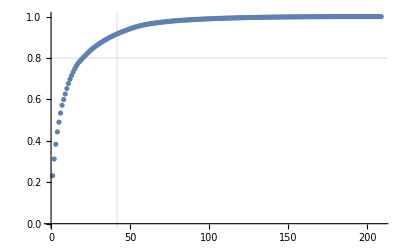

```mathematica
t=Reverse@Sort@gdps⟦All,2⟧;
ListPlot[Accumulate[t]/Total[t],PlotRange->All,GridLines->{{0.2}Length[t],{0.8}}]
```

### TunnelData -- exaggerated Pareto law manifestation

```mathematica
tunnelLengths=TunnelData[All,{"Name","Length"}];
tunnelLengths//Length
```

1195

```mathematica
RecordsSummary[DeleteCases[tunnelLengths,{_,_Missing}]/.Quantity[x_,_]:>N[x]]
```

{1 column 1
Sozina Tunnel | 2
149th Street Tunnel | 1
63rd Street Tunnel | 1
Abdalajis Tunnel | 1
Adler Tunnel | 1
Aegidienberg Tunnel | 1
(Other) | 1178,2 column 2
Min | 0.428746
1st Qu | 1.00631
Median | 1.7267
3rd Qu | 3.25863
Mean | 29.7326
Max | 2132.55}

```mathematica
t=Reverse[Sort[DeleteMissing[tunnelLengths⟦All,-1⟧]/.Quantity[x_,_]:>x]];
```

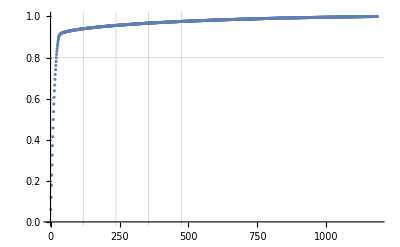

```mathematica
ListPlot[Accumulate[t]/Total[t],PlotRange->All,GridLines->{Length[t]Range[0.1,0.4,0.1],{0.8}}]
```

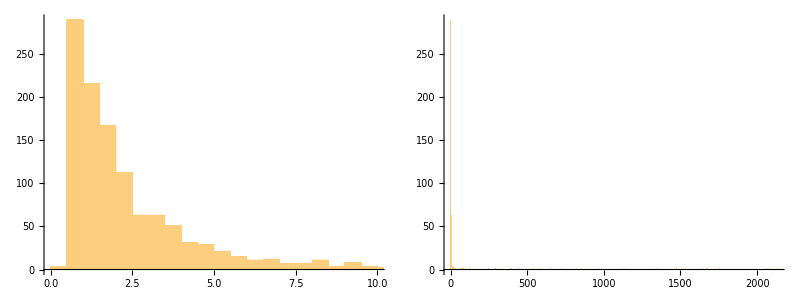

```mathematica
Grid[{{Histogram[t],Histogram[t,PlotRange->All]}}]
```

### BridgeData -- compare with tunnel lengths

```mathematica
bLens=BridgeData[All,{"Name","Length"}];
bLens//Length
```

914

```mathematica
RecordsSummary[DeleteCases[bLens,{_,_Missing}]/.Quantity[x_,_]:>N[x]]
```

{1 column 1
Beaver Bridge | 3
Broadway Bridge | 3
Champlain Bridge | 3
Bidwell Bar Bridge | 2
Blue Water Bridge | 2
Centennial Bridge | 2
(Other) | 734,2 column 2
Min | 39.3701
1st Qu | 1308.23
Median | 3818.9
3rd Qu | 7578.74
Mean | 10032.5
Max | 540682.}

```mathematica
t=Reverse[Sort[DeleteMissing[bLens⟦All,-1⟧]/.Quantity[x_,_]:>x]];
```

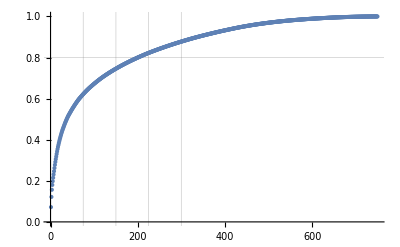

```mathematica
ListPlot[Accumulate[t]/Total[t],PlotRange->All,GridLines->{Length[t]Range[0.1,0.4,0.1],{0.8}}]
```

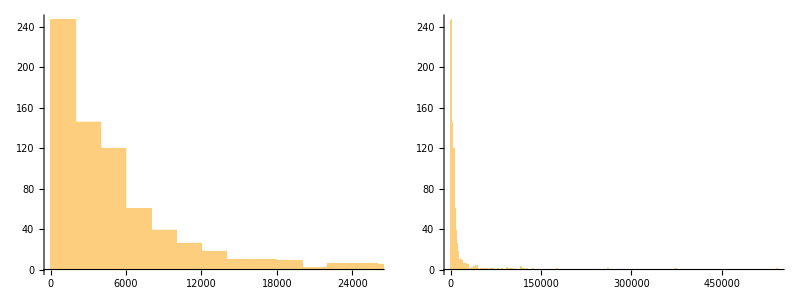

```mathematica
Grid[{{Histogram[t],Histogram[t,PlotRange->All]}}]
```

```mathematica
bCls=BridgeData[All,{"Name","ClearanceBelow"}];
```

```mathematica
t=Reverse[Sort[DeleteMissing[bCls⟦All,-1⟧]/.Quantity[x_,_]:>x]];
```

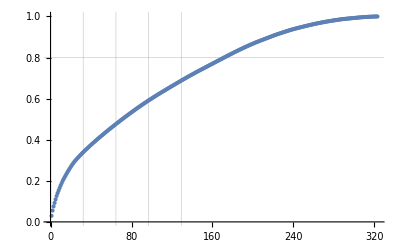

```mathematica
ListPlot[Accumulate[t]/Total[t],PlotRange->All,GridLines->{Length[t]Range[0.1,0.4,0.1],{0.8}}]
```

### Further examples

Pareto law adherence examples.nb

## Pareto law adherence examples with other data

### Most popular pin codes

http://www.datagenetics.com/blog/september32012/

### Online retail data set report

Taken from https://archive.ics.uci.edu/ml/datasets/Online+Retail .

Report link :  “OnlineRetail-StatisticsForTransactionsDataAndRelatedSMR.html”.

### Retail stores (time series)

Obfuscated data from a retail company. Log plot of time series over different stores.

### Music industry

Here is the Pareto Law adherence plot of a snapshot of big music distributor.

### Movie recommender

This is an interactive interface to a MovieRecommender based on a bi-partite graph.

For an example of the bi-partite graphs this recommender works on see the neat example in this blog post: “RSparseMatrix for sparse matrices with named rows and columns”.

```mathematica
Import["https://mathematicaforprediction.files.wordpress.com/2015/10/movies-actors-graph.png"]
```

-Graphics-

## Pareto law adherence utilization

If we see that Pareto law manifests in the data we can utilize in several ways.

Restrict the dataset to only those items that are in the top Pareto fraction.

Create tests based on the Pareto law. Those kind of tests would have better statistical power and be more indicative of what is going on.

Investigate under what conditions the Pareto law manifestation is less prominent. This can be used to judge recommenders performance.

## Algorithm selection

### Linear vector space representation

It is always possible to do such a representation at least to a point.

### Fit data to the algorithms

## Categorizing the numerical variables : basic

Here is a mosaic plot for the dataset “Titanic” without the column “passenger age” (which is not categorical):

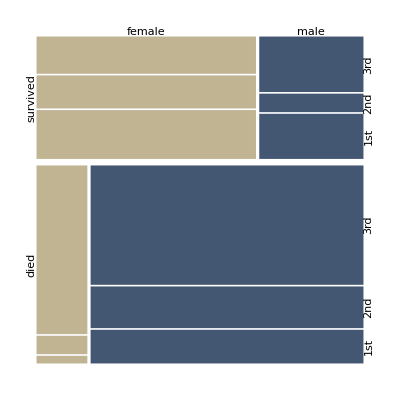

```mathematica
MosaicPlot[titanicDataset⟦All, {4,3,1}⟧ ,ColorRules->{2->ColorData[7, "ColorList"]}]
```

Here is the distribution of the passenger ages:

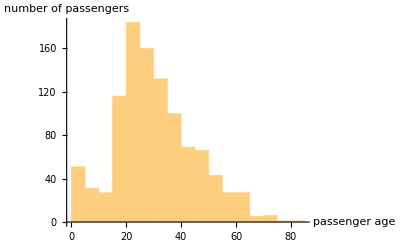

```mathematica
Histogram[titanicDataset⟦All,2⟧,Automatic,AxesLabel->{"passenger age","number of passengers"}]
```

One way to visualize the survival dependence of age is the following.

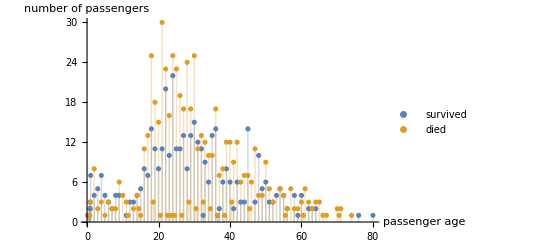

```mathematica
ListPlot[{
Tooltip[Tally[Pick[titanicDataset⟦All,2⟧,#=="survived"&/@titanicDataset⟦All,4⟧]],"survied"],Tooltip[Tally[Pick[titanicDataset⟦All,2⟧,#=="died"&/@titanicDataset⟦All,4⟧]],"died"]},Filling->Axis,PlotRange->All,PlotLegends->{"survived","died"},AxesLabel->{"passenger age","number of passengers"}]
```

From the plot we can see that age-wise more or less survival and death followed the distribution of the ages of all passengers.

At this point it is better to turn age into a categorical variable and visualize with a mosaic plot. One way to do this is to use quantiles of ages; another is to use predefined age ranges. We are going to use the latter approach.

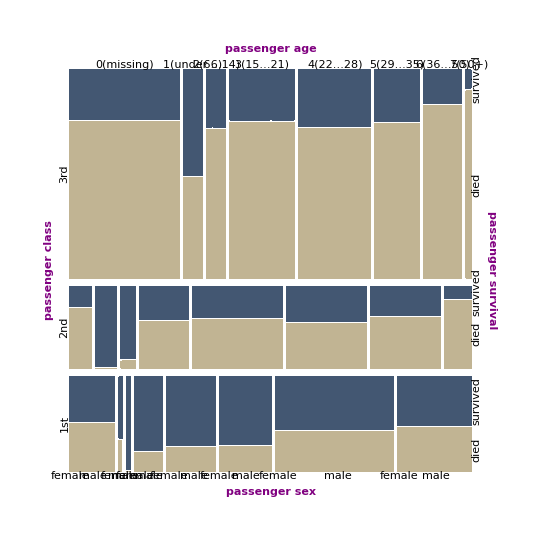

```mathematica
titanicDatasetCatAge=titanicDataset;
ageQF=Piecewise[{{1, -∞<#1≤5}, {2, 5<#1≤14}, {3, 14<#1≤21}, {4, 21<#1≤28}, {5, 28<#1≤35}, {6, 35<#1≤50}, {7, 50<#1≤∞}, {0, True}}]&;
titanicDatasetCatAge⟦All,2⟧=Map[If[MissingQ[#],0,ageQF[#]]&,titanicDatasetCatAge⟦All,2⟧]/.{1->"1(under 6)",2->"2(6…14)",3->"3(15…21)",4->"4(22…28)",5->"5(29…35)",6->"6(36…50)",7->"7(50+)",0->"0(missing)"};
MosaicPlot[titanicDatasetCatAge⟦All,{1,2,4,3}⟧,
ColorRules->{3->ColorData[7,"ColorList"]},
"LabelRotation"->{{0.5,0.5},{0,1}},
"ColumnNames"->Map[Style[#,Larger,Bold,Purple]&,titanicVarNames⟦{1,2,4,3}⟧]]
```

From the plot we can see that the very young were much more likely to survive in the 1st and 2nd class. Note the large amount of missing ages. The missing data might be one of the reasons “passenger age” is not that decisive.

The conversion of “passenger age” into a categorical variable is also useful for the application of Association rules and topic extraction. (See [4, 5].)

## Categorizing the numerical variables : time series

### Data (temperature in a given location)

```mathematica
location={"Atlanta","GA"};
(*location="Melbourne";*)
tempData=WeatherData[location, "Temperature",{{2010, 1, 1}, {2016, 3, 12}, "Day"}];
tempData//Length
```

4

```mathematica
tempPData=Partition[Normal@tempData["Values"],2,1];
tempPData=tempPData/.Quantity[q_,_]:>q;
tempPData=Select[tempPData,VectorQ[#,NumberQ]&];
tempPData//Dimensions
```

{2257,2}

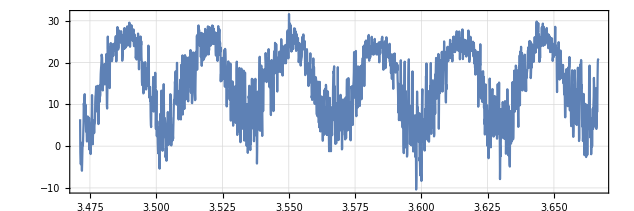

```mathematica
grDLP=ListLinePlot[tempData,PlotRange->All,AspectRatio->1/3,PlotTheme->"Detailed"]
```

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/QuantileRegression.m"]
```

### Predict today’s temperature from yesterday’s one

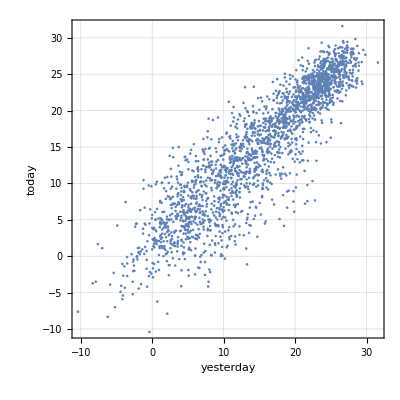

```mathematica
ListPlot[tempPData,PlotTheme->"Detailed",AspectRatio->1,FrameLabel->{"yesterday","today"}]
```

### Basic categorization of the time series

Let us look at the results in the previous slide from a different perspective using mosaic plots.

```mathematica
tvals=Normal[tempData["Values"]]/.Quantity[q_,_]:>q;
```

Make a piecewise function using a grid of quantile values:

```mathematica
qvals=Quantile[tvals,Range[0,1,1/11]];
qrf=QuantileReplacementFunc[qvals];
```

Make a piecewise function using a uniform grid

```mathematica
rvals=Rescale[Range[1,12],{1,12},{Min[tvals],Max[tvals]}];
rrf=QuantileReplacementFunc[rvals];
```

Compare the tow labeling functions:

```mathematica
Grid[{{"Quantiles grid","Uniform grid"},{qrf,rrf}},Dividers->All]
```

Quantiles grid | Uniform grid
Piecewise[{{1, -∞<#1≤-10.39}, {2, -10.39<#1≤3.06}, {3, 3.06<#1≤6.11}, {4, 6.11<#1≤9.56}, {5, 9.56<#1≤12.22}, {6, 12.22<#1≤14.83}, {7, 14.83<#1≤17.78}, {8, 17.78<#1≤20.22}, {9, 20.22<#1≤22.22}, {10, 22.22<#1≤23.83}, {11, 23.83<#1≤25.61}, {12, 25.61<#1≤31.61}, {13, 31.61<#1≤∞}, {0, True}}]& | Piecewise[{{1, -∞<#1≤-10.39}, {2, -10.39<#1≤-6.57182}, {3, -6.57182<#1≤-2.75364}, {4, -2.75364<#1≤1.06455}, {5, 1.06455<#1≤4.88273}, {6, 4.88273<#1≤8.70091}, {7, 8.70091<#1≤12.5191}, {8, 12.5191<#1≤16.3373}, {9, 16.3373<#1≤20.1555}, {10, 20.1555<#1≤23.9736}, {11, 23.9736<#1≤27.7918}, {12, 27.7918<#1≤31.61}, {13, 31.61<#1≤∞}, {0, True}}]&

Compare the mosaic plots corresponding to the two labeling functions:

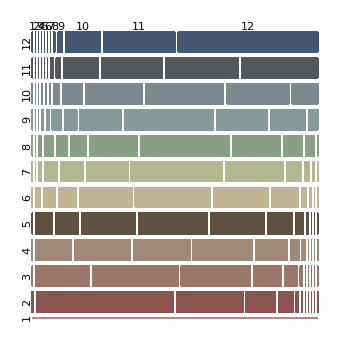
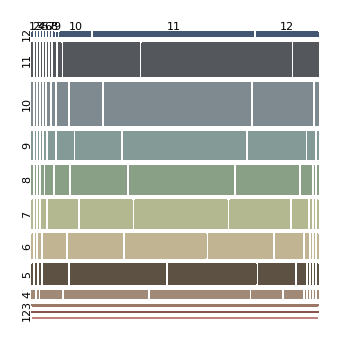
Quantiles grid | Uniform grid
-Graphics- | -Graphics-

```mathematica
Grid[{{"Quantiles grid","Uniform grid"},{MosaicPlot[Map[qrf,tempPData,{-1}],ImageSize->350],MosaicPlot[Map[rrf,tempPData,{-1}],ImageSize->350]}},Dividers->All]
```

Obviously, we can apply other sequence mining algorithms. E.g. Markov chains.

## Categorizing the numerical variables : time series 2

```mathematica
tempDataArray=Transpose[{tempData["TimeList"]⟦1⟧,Normal[tempData["Values"]]/.Quantity[x_,_]:>x}];
```

Find regression quantiles:

```mathematica
qs=Join[{0.02},FindDivisions[{0,1},6]⟦2;;-2⟧,{0.98}]//N
qs//Length
```

{0.02,0.2,0.4,0.6,0.8,0.98}

6

```mathematica
AbsoluteTiming[
qFuncsDLP=QuantileRegression[tempDataArray,26,qs,Method->{LinearProgramming,Method->"CLP"}];
]
```

{2.32459,Null}

Plot regression quantiles and time series data:

```mathematica
AbsoluteTiming[grQFuncsDLP=Plot[Evaluate[Through[qFuncsDLP[x]]],{x,Min[tempDataArray⟦All,1⟧],Max[tempDataArray⟦All,1⟧]},PerformanceGoal->"Speed",PlotPoints->130];
]
```

{6.67471,Null}

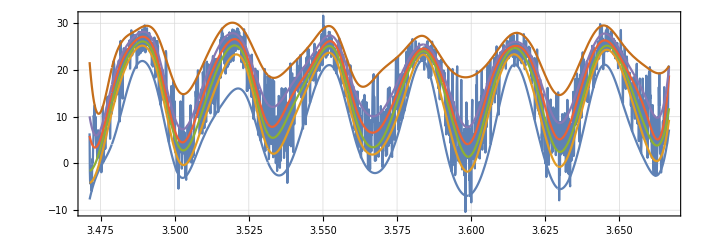

```mathematica
Show[{grDLP,grQFuncsDLP}]
```

## Categorizing the numerical variables : time series 3

### Combination with sequence mining techniques

Let us extract states from the fitted regression quantiles:

```mathematica
FindQRRange[{x_,y_}]:=
Block[{qfs,pfunc},
qfs=Through[qFuncsDLP[x]];
pfunc=QuantileReplacementFunc[qfs];
pfunc[y]
];
```

```mathematica
qstates=FindQRRange/@tempDataArray⟦All⟧;
```

Here is how the state sequence looks like:

```mathematica
Shallow[qstates]
```

{5,3,3,2,2,3,4,2,1,2,«2248»}

Here is the mosaic plot picturing the conditional probabilities of the state occurrence:

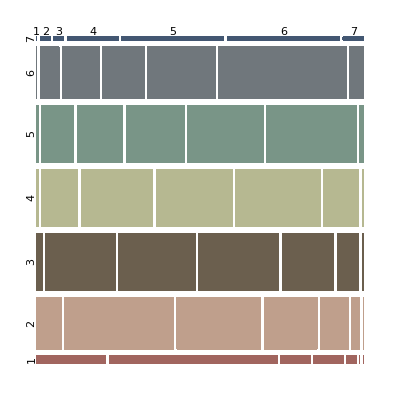

```mathematica
MosaicPlot[Partition[qstates,2,1]]
```

## Categorizing the numerical variables : time series 4

For somewhat orthogonal alternatives see “time series motifs mining”.

## Dimension reduction

We are going to compare these dimension reduction techniques:

Thin Singular Value Decomposition (SVD)

Non-Negative Matrix Factorization (NNMF)

Independent Component Analysis (ICA)

### Mathematical formulations

Consider a document × term matrix A then thin SVD and NNMF would give

W H≈A

A∈ℝ^(documents × terms)

W∈ℝ^(documents × topics)

H∈ℝ^(topics × terms)

The closeness of approximation is done by minimizing (‖A-W H‖)_F.

Full SVD can give  U S V^*=A.

For NNMF we have W_(i,j)≥0 and H_(i,j)≥0 for all (i,j).

SVD decomposition gives unique directions of the new bases. NMF does not give unique decomposition, it has to be repeated several times.

## Comparison between SVD and NNMF by example

### Generate low dimensional data

#### First set

```mathematica
pnts=Transpose[Table[RandomReal[NormalDistribution[RandomReal[{3i,4i}],RandomReal[i{1,3}]],600],{i,3}]];
pnts=pnts.RotationMatrix[π/4,{0,1,1}];
pnts=TranslationTransform[{1,2,3}]/@pnts;
```

```mathematica
With[{c=20},Graphics3D[{Point[Join[pnts]]},PlotRange->{{-c,c},{-c,c},{-c,c}},Axes->True]]
```

-Graphics3D-

#### Second set (assigned)

```mathematica
pnts={{-0.7403060787538136,7.845774593331143,9.535755420045536},{0.6462578450890701,4.494295647078985,12.128970490501214},{-7.376049945044078,4.111371123867969,11.334506430098513},{-1.9795261790256142,5.856570970699572,9.040092072468626},{6.163021806061327,6.494818272844803,12.314248163775842},{6.259196406599997,7.86151524817697,11.916555237011474},{5.233080895593769,7.907582019770303,12.190791644821285},{-0.4536189684489118,6.112841373339269,8.226612344776466},{8.633411386550046,2.8995772358333953,18.0985367760456},{-4.152139956809677,9.471222861661191,7.609192805605511},{2.37704738183494,8.33610568819885,9.73587501361768},{4.96303842259793,5.536092079855351,13.91714628673611},{0.6378320474483257,2.964399304930481,16.44335166466011},{4.198278648904084,8.488733367766994,9.967604918331666},{2.3665763966658755,10.975186456627114,7.440876979139132},{5.005102290853596,5.149150066991728,15.395437413453354},{-0.3087104151621709,9.292112915433052,7.610032437972928},{-3.642565825513977,5.898777589516036,10.496023371310056},{-0.8431994847214868,4.835949309255406,12.765421799811115},{4.46179715082922,9.351247561850377,11.216237904582332},{-3.7670262929052054,5.795298577219147,9.581972329747313},{7.715980577718073,-0.5277959105797514,20.511966805498574},{-4.410860995631163,4.252302806774226,11.083631433403779},{5.21037129701279,4.296768960747356,13.827428647918781},{-1.8625448280372336,7.14894781916528,10.372559506020231},{4.638439824588561,7.3165028180086225,10.673599381951718},{5.724391846891992,6.91463520574335,15.1633000948982},{-3.5391549668366196,4.090356825713278,11.471543452502509},{5.712702093396405,6.107839382022464,15.22475375934727},{6.541722897278265,8.902517205430572,10.764949519736962},{-1.753249115750783,8.609295260660847,7.91360855535279},{3.93369931729279,5.036974176194978,13.013702807674642},{-2.1454652627646094,6.96597536968639,12.505420149024147},{-0.09537970146080887,5.133261171692347,12.516462340989117},{2.5156468852136635,3.3349825520336713,14.670716595926837},{2.1552077450518423,5.65868334034192,11.288451245952501},{7.691774298692732,8.931542423546649,11.730934771446407},{3.469267514162751,8.179666843910411,10.955597847530957},{2.920248544421746,5.309656651011858,11.085435111506078},{1.6183566647312335,7.729034099888408,9.59756159160214},{1.8188853505191265,5.054289643104148,9.505729661741082},{-0.7976045697504648,5.251159549555657,14.609558739151861},{1.778929734344648,1.8791334265398305,15.668250225457342},{2.142681065927704,5.6048379595470434,11.871234862740032},{2.932343041544131,7.859119319218362,11.531484341988042},{-1.1145084990102085,6.990008373675742,11.28212405169382},{2.1713824385655114,4.387084306772537,13.870109698968918},{6.158173850779895,5.913150589787923,15.603738890154236},{6.364367466241298,3.873196409821979,14.596656816182263},{-6.4893344926100305,5.542726903217593,8.21058879950239},{1.0358577379267526,7.449745976764981,10.770011807602563},{-4.623601961200826,6.143247878853979,7.713039785164409},{-2.9523629351036735,6.785377571511794,8.180837360813001},{-0.08908774519107743,1.977271783743241,13.870931329898951},{4.744213353799306,3.366244244521927,17.046960519722987},{-6.511157579837878,5.667212232599891,6.933552960801933},{-5.7906543126356205,8.127921487016739,7.880046955516824},{-1.580557094271759,6.432298107969255,12.740358522860468},{-0.17462948865243888,0.006097509170299276,18.18013131355697},{7.6617788571264125,1.0776072315492176,18.08196688327419},{-2.416865062948633,3.0315010904042388,10.85610924150274},{-5.446777067594179,6.002380772132152,8.70924854623698},{4.348911165954868,9.099367582370704,9.843462568721158},{3.4162149166391806,3.643223080108572,14.742852858790817},{6.739448452255419,6.540359893662762,13.640772852812498},{2.4344270265985655,9.461710574933605,7.046674834274348},{4.132276056995028,7.868947462542589,13.930622644319598},{5.67551690613176,9.413533207350946,11.040650451332862},{-2.9354949895331153,7.7653443426535915,8.530502070341349},{3.9572667065013856,10.776425043378932,7.920150853214942},{1.3961189851029507,9.428525287359273,8.184866400310208},{5.334228008341013,4.110043788609669,15.715254852981797},{1.1528859212235512,8.341724327165819,10.788110825541395},{8.515961962396847,4.000007949620292,18.410063449535105},{-2.60649877652894,4.608141239388997,11.697453350102913},{2.8776507059693976,3.6349077646948453,14.96097937906908},{2.221750723870481,0.5172407583471337,16.175351604272542},{2.907885292360431,5.116915544247162,12.436796296730176},{4.28376049773224,4.301386991865764,14.869573475491384},{3.2725683979021127,4.898567242980626,13.12985982736971},{3.0508930887352195,3.847673198229955,14.879012919429712},{1.8242621154754923,5.165656156571481,13.482263257204181},{-1.4433262895548125,5.4979771344644845,12.22651538282939},{6.515501769938406,7.179615734312273,13.14224467975825},{-2.8805786518173813,6.084797109964347,10.78558135957363},{3.403750470395595,4.1668348889893405,12.388756970433082},{-3.8402705331311178,2.6387060493808168,13.712771684190173},{-3.0873957944841397,9.194195086613597,7.060646496502024},{0.4264528221863988,6.33910334938907,11.085039419244216},{-0.9043356904359245,2.7660878448997543,14.144292669327044},{2.384772928195726,4.867852088203252,12.898623340603447},{2.6739920120582985,1.4946236938665525,15.278139201183986},{4.186425921678696,8.78924666045559,10.02943900251463},{2.1802169103526676,11.833542294094793,6.865604541008603},{1.5374355056836828,7.2028769461559845,8.715157143132206},{1.3015779966580077,6.312664760105232,12.967910983932589},{2.052082010633803,4.835052363606848,13.176651242225288},{-0.8632824852718342,4.7073265572914496,12.302422248739244},{-1.1303729434717944,5.755403785854568,9.165165252638879},{0.029225491195785658,6.644147924510101,10.521444529250068},{3.1460621481013034,4.205931352679263,14.730689671600617},{5.210016718337929,9.30390461924162,11.071752360536763},{-4.654328538539237,4.462062802014692,11.252847941388765},{0.9085157615629247,-2.1252919990704013,19.571624814411216},{3.8207415409979326,2.4794366198987916,16.562451264349786},{2.976758721988026,0.19878391883311064,17.688494481595825},{2.521261659431284,2.6253620346607023,12.580690571132859},{-0.8345467881388262,2.4896119400542807,12.722068274457591},{-0.9689492731678642,7.950490502796477,5.304420473047304},{7.418060351717688,4.467396156609631,14.421923149844023},{-0.9406298458716393,6.405678035532177,12.05906282641228},{6.36150048928855,3.4616637595692974,13.931342900258679},{6.349157553635473,5.260221690565657,14.591061379435136},{-0.9396309106833232,6.55170074593088,11.037806720403356},{0.835821441233259,6.675829305350721,10.923574286484554},{-2.3092482628153235,7.510438183382431,8.018833166912895},{2.8381570136580256,0.5979783227250586,17.364780421835277},{-3.632621836429329,1.9095709108103138,12.190465052858322},{4.182038067730945,6.555699777972533,10.131233482514524},{3.6288389743142715,5.517846022958313,12.54757254814523},{0.6865015402671757,2.596585040466672,14.877794653212675},{2.2219323088012453,6.937901742198992,9.821394413115982},{6.123573325030077,10.118510072409961,9.402900692746856},{2.645118378699327,3.9879156681083687,17.389094439597017},{5.8477430861915005,2.7671309889529097,14.66915899658137},{-1.3899705870281798,7.324031608992515,9.653187867238493},{-0.8050682243616736,3.950644739655953,11.489262572484538},{4.906435412248053,6.692170851650894,13.72470399861138},{1.6104650687086077,1.3786198781636818,16.18668015884633},{0.843630372698084,8.824900874665817,9.019792963425193},{1.694437219737444,9.332340127912676,9.156584031095033},{1.6626728845754402,2.5955632170789524,15.343966433515476},{0.41930983917830034,7.090229450174345,12.586192906169778},{-0.3966762165726081,11.70922418308809,3.1392276254858675},{4.8392722283580465,3.480951257439111,16.097930300518428},{-0.8345809627408594,6.838768629627602,10.272088190790093},{0.47069663732398137,5.074656143900331,12.316833623492059},{-1.0520615498027528,10.596262711644643,6.465474039565118},{1.899394114998568,2.573536288653414,14.61101879984368},{4.36620840145782,3.3212061594450386,18.29855873972096},{2.229692036727299,10.512093612367304,8.499544756270538},{-2.255437574620953,6.456989216305327,9.977126789501563},{2.427394836054222,7.5396283730211415,10.188467802232548},{-3.5732514274554688,6.3451920279846,9.170724627769951},{-2.031434582488092,3.892175327783693,11.949822597241827},{1.9191149243546808,12.427133602870086,5.6732871234672215},{2.012512695188888,14.157855615657247,5.753853013613904},{2.803330669328138,5.354602374651012,12.281032468974594},{-5.362290447665538,6.235327896400484,7.958109681368832},{10.17716894269766,6.386793465218414,16.382143765834577},{-1.4002089646104485,9.079267988417007,7.648622431368047},{3.947637859043377,2.6135818528571235,16.039494574991057},{10.70640967137588,4.670651466563308,16.142265491662826},{6.528772253295539,4.393127632685218,16.721503940966358},{3.406476151033309,5.775162284297216,12.865491646471344},{6.643826300528496,3.786247592225659,15.823194983284557},{5.370610244388392,6.952710829133056,11.643064536392844},{1.7443087910774544,5.403328275633236,13.255508216325481},{3.6073791150289223,7.100910482761617,12.59124303910577},{1.6482694904602733,7.29308663916082,11.708556838715914},{5.091226391946858,4.346492813753312,15.074262298915585},{-0.1222057790306268,2.2574029187425753,16.487857919074663},{-3.481406536111332,1.8670254024882835,13.652274186876559},{7.531104501080364,5.32482318823263,15.155467936784405},{0.06290859941613913,5.667241348917542,9.876112041846609},{2.2922750250643795,6.124498958799645,12.658375153504377},{3.5120446858576484,-0.09687049732323061,18.838600397329987},{4.092165490535653,8.71784688898925,11.699550817650952},{-1.842541678288138,4.842400479812431,9.426778318589696},{2.080273937464501,4.294761785076594,13.497032971344604},{5.311092639204224,4.7526680019715455,16.09881696513524},{2.9737722595715086,1.9743662017964532,19.364024535079267},{0.32479109352800295,7.288952050672921,9.051236383357063},{2.349367044891926,4.430768833990366,13.478963090833059},{-0.2495125574057555,0.5092341323164566,14.022286105406021},{-0.7547764559687486,1.6219304783138648,15.036336257978908},{0.40467189795868297,5.848654097449938,11.389939834557083},{-4.09689679308865,10.220400966694577,7.0972187309320445},{0.9392778098836407,6.400573879889079,10.115936719235497},{3.0902990838194877,5.836900899399075,13.152638800075737},{2.441810090421619,4.87051209058943,14.846235558108768},{-0.23310442873434134,7.189474614391315,9.799012943191844},{0.9022787104372387,6.311987050558878,12.457265207765387},{6.017047100822999,9.358895302418407,10.358556353445652},{2.6994876365901943,7.9585150570774745,13.871130067210512},{6.510956417383151,5.64990859594816,14.036323394024839},{2.9379716730157304,8.534297556809786,9.572187378606149},{-2.0609548186249955,8.100038157958778,9.16946652300987},{0.6666605846514697,-0.825160513283004,16.929980257569778},{-1.1711564477570033,3.5527957151627203,11.053960161756903},{-0.34780699145864125,3.566906204125216,12.976211478178367},{1.7154921763256183,5.855121206961016,11.569867497181129},{8.575726471985071,5.872897628142669,16.729605875059143},{5.886645285321459,4.638778940479566,16.80562288452525},{2.043856647997966,9.578604319628507,8.129269644202711},{2.4261119391716592,4.206441268809557,13.616991637152523},{12.116946568101904,4.680965361082507,18.48650249906694},{4.3067769541170655,7.806886760559793,11.9407889391733},{3.169484582698301,7.706625666001704,11.439615425444867},{-1.909013626888779,7.544196223341978,10.347702156151183},{0.1330700929966131,5.674528332429601,11.448187967405218},{4.549607386926803,3.4432166508086084,17.144528383923493},{11.797162254782364,6.594960352905367,17.901683214988772},{0.9421707370040124,2.8029849873077586,11.8671627902465},{-5.072038634883273,7.173860244354115,6.369629932061993},{-3.024859540224692,8.033852874529883,9.628275943477508},{1.122096427254407,0.8277875783062845,18.22606055249078},{2.0457588778648095,11.20728049608148,9.09568026251725},{4.099092793120907,7.044840252308574,11.770127480271437},{-0.26839102890428856,8.247989013655966,7.773018526422738},{-1.5554366947663159,7.689067502590599,10.593023493507046},{2.3981785566970792,8.398137629415109,9.963348506792947},{2.235908704124631,8.266485718619126,9.789537318173434},{2.259051758702201,3.3591506127975013,13.692053565375486},{-2.1957090557301817,3.4786860706240548,12.339670453089976},{3.6951896087717255,5.000180886038866,13.0300244901631},{1.3483208476554527,-1.1886115167656364,17.770578137806243},{-5.13685844081046,4.2385533703966045,9.254192674302532},{1.2627384572280294,6.419581716426897,8.410380934233265},{2.320929326260181,4.817296093879291,11.697121604821302},{-1.7327358842073988,8.322307501078129,7.57645677039303},{8.70496744229127,7.1031943631425705,14.758467250336523},{-0.05389223361450224,5.019918640915762,12.240788231104947},{1.8091982513931484,5.1378170670907855,11.322048066305314},{4.249939428891729,1.0715887327975384,16.64033186383009},{1.348514430736481,8.229015127199641,10.679858084206922},{2.553450384732619,8.311019630239592,7.987818825678498},{5.732921601942866,5.662534256133679,13.626851325541807},{-4.480487916796985,4.60201095992636,10.136576308545102},{8.990669671665552,2.680984148230763,16.524314592464215},{-1.2065613968882452,3.443005794403863,14.36992882202929},{-3.8740000755496404,5.740728605794081,9.787545850803099},{4.65346412109233,4.413328974779038,14.811840378362245},{8.23398005333057,2.9226116149679915,16.56523653161342},{1.0267164066307704,8.929277987133895,6.678332453171915},{-3.1577316791948276,8.751020352585163,7.149722716714054},{8.335913985176264,7.773759028498483,16.409382507992966},{2.639790064154361,7.157050167720045,11.216531239676478},{1.026052878760801,7.157898719615191,12.308848605165176},{3.1500015123120457,7.453747767845009,12.888109256193392},{2.642551227874808,4.393375060173593,15.466763683265249},{3.1966409312464252,6.550340264428587,9.964248007675874},{-1.159470117608433,5.249141821827465,10.10596442204973},{-2.8661579454122372,5.8231583219202365,11.495224506897006},{4.029224033504034,2.729550779120739,16.66810887378898},{-0.5021896351652355,1.9475094523721825,12.545424445060265},{9.710455270725967,6.380605806468985,17.26760006194604},{4.5315231758511345,7.280073358703728,12.192544221456592},{-2.4751180264928783,7.038839850183885,8.865254162799793},{-6.164257488499901,4.367804826692785,9.439065049904016},{-0.6960244830480837,7.472839000005101,9.89642157167745},{3.042789942339018,3.4455510255106336,15.400756125473128},{1.6639484194040133,0.5331981182460837,18.383083032462316},{5.940510257363815,4.8325986514138375,15.056966831379029},{5.578175685363484,8.265932296727602,12.569304521114102},{-3.0732316385872522,1.8723789468324235,13.133539105421466},{0.7399641513158075,3.0793505806886277,14.218731505186991},{-0.6780053782013655,4.218093451488198,12.215987724156786},{-1.937914275442639,4.775414491470954,12.755683086549631},{4.719241691734102,6.85961681607073,14.004174393571956},{-0.6291112497626932,1.2320929136310808,15.954649504732076},{-0.1839244196278047,7.089030416174677,10.66211870638651},{8.527170483732142,5.867659788240872,15.434794727118673},{0.8500246445918309,6.262132437667427,13.96428518976524},{2.9048210174571527,2.1469139762118887,15.50221959506613},{1.9103047936308855,1.6386975101859322,17.345797098322123},{0.9235755702862978,9.007062100869444,9.55764094047818},{4.004926206569136,3.3682429879927773,12.68885006619055},{-0.43380125666947666,0.6917519557554437,14.651846052542885},{5.085750556400378,7.9477000957803465,10.843770759986631},{-2.689624829768558,8.110768682805398,4.946715283270123},{0.9187034309204276,4.39889890500345,13.625146024026336},{-2.959556870066329,6.768212594654649,10.819814393871646},{2.015530393290924,3.7444978553666637,14.382802636784778},{7.320970855663513,7.506836603313919,14.155572262838794},{1.4242944170670135,6.71680704865492,13.411315169514797},{3.441084632542717,9.22175519750764,9.821723266779044},{2.2374876398898307,7.918205561636389,11.580195802626825},{-0.3380422462272983,3.032539691973226,14.296270889489726},{0.744689638154497,3.559369357207503,11.540229183791697},{-2.6487474004559783,5.504552270056472,11.207684549465586},{-4.208538666052307,1.2119073932597537,12.520355147436682},{0.00006497031420948929,6.370271518188526,13.354532235609039},{-1.2964463441900582,6.994136236313534,9.115877749090071},{4.924405885664912,4.409989696902832,13.719377174525757},{-2.02772793417566,1.0799384721708511,14.066941975572853},{-1.6177810771136274,5.754942888367334,11.079572933446256},{6.201371894615397,5.209848102231472,15.436213803343923},{-3.3012638182922984,9.345044901568166,4.931437268515415},{-3.15528461651767,3.4718249973480075,12.570378210260063},{1.2438106456683045,5.479178452379556,11.950127159121779},{2.5546019321629236,4.84692514512499,11.217659856174713},{4.485192518269013,2.3313347982676333,16.29359730763574},{-2.578971663190271,7.156144483603883,8.862535547664937},{5.600774921204471,-0.40119399787626975,20.321113391046957},{-3.888430192297246,1.6434931778966373,12.737966194860569},{-3.084093434637201,2.349835361291884,10.710540625805189},{-4.066773205519875,3.314691285867677,11.2334211256039},{1.297315375308317,1.9212755499495389,15.01305917663625},{3.1161147914616785,5.514817837765124,12.88588564476892},{2.227086951773166,1.0417350102866187,15.852527049612116},{-4.462707275436992,1.3527858221197997,11.952649199731528},{1.033847817623463,0.20823695508499718,17.853623850248756},{4.071167021470014,3.4692034257494075,16.57684486079074},{4.897373253210615,6.144611514149949,11.885288494276296},{-3.945862395307634,7.595058268514963,9.827229171823014},{-1.9696837754813452,3.6041148340671167,14.817780825826938},{6.094786401960741,7.3871631589450075,13.53999243478189},{-1.5768424331835056,8.569981594137591,7.089770254965528},{1.946556082677474,10.505997222654416,9.464761221122707},{-1.2329049488289958,7.767248005516334,11.136659426685195},{3.1871481758861147,6.081049085979125,11.130646382026406},{1.9366626432691971,8.466607788245017,8.085941179430186},{-1.4651264399753927,10.419680673090374,6.074110659617796},{-0.3105836281430441,7.347378824612626,10.51306828922237},{-0.2936255528564993,7.728540924106645,10.631151971366702},{0.526832139255422,8.731104177125893,8.675449598323082},{-9.09323299993329,2.3997736180130675,7.0345216613594985},{3.302299817393105,6.365075027866213,9.419971693026934},{5.789667175738278,2.6692373420083015,17.67584572476182},{6.0078180058987884,10.547716803761558,8.307349911527075},{9.019348275449465,8.40787459546273,12.544901506197322},{1.4555423333735482,9.636967039664903,5.648990797082773},{-3.0726919150666774,5.184929019048111,7.146493114106421},{4.4689875623818915,-0.34075096396205495,21.106671402091898},{-1.3688420321646588,4.722900507525862,10.565437920914615},{-1.6945718275089319,2.8301343636339764,13.401281172318257},{-4.112430113587652,7.622755020563822,6.269347322879648},{-7.260894446029795,5.513611699003247,10.094866509244154},{-3.4307699052982628,1.7912936648251332,14.628605947419985},{4.683452077651664,7.545891973659971,12.213982416537496},{1.7340866227622573,4.143914642500882,15.110864160536753},{4.820744861821481,7.170353584005263,10.02957580872613},{6.373229917593539,3.6852564777459142,14.016090302469227},{-5.3532007296663995,6.5372729265515375,8.130641925739026},{-0.31738494016480967,7.791966639338745,9.238888983389888},{4.3219238762037095,6.939992739837741,15.020058674329476},{-1.1872019706060968,1.60201813635579,15.51473997456812},{1.3989390444168146,5.285526007110542,11.798737903200216},{1.5549208057552457,6.5825687149914875,11.53574471050827},{-1.8582171556135063,3.778593276984899,12.329250530036465},{-2.6922350999467985,6.7242034976356955,7.520786567993904},{3.6053409212448804,3.374755268631013,15.87649824128265},{-5.497031129764865,1.5620714063050594,14.943957482566798},{3.8816057826136605,3.2395278378898293,18.399421088933067},{-0.26226774834025024,7.004643296290033,10.335965300649498},{-1.1207790344706483,9.382875127112209,6.481986968524986},{5.05129460645836,4.15825295266257,13.623693758140476},{1.1493704548145738,11.846445174451937,6.895015253081178},{-5.15779727262891,0.666834541340303,15.244499413108244},{-3.1457678786925434,1.0156437039503388,10.993056126482607},{-0.07757230006541738,3.8079439292214348,11.011151104032518},{-2.4772228864384322,4.388738257448232,11.446724167593736},{4.44519917334507,4.824632582548654,13.323494233951674},{1.876469434788632,9.047371740054508,11.318128597902827},{0.9879163474766965,3.3716321977207206,15.439265444121718},{6.098204991540063,5.699856104050848,13.626813309282646},{0.8158574238454017,9.153840925070448,6.857937229782664},{1.6658124484532957,7.7735302902742145,7.965671346707698},{1.9245367844966212,1.3949865136670052,14.561593794877009},{3.2086649888612193,6.025578430630404,13.383937857171293},{-0.2736009866023248,4.257150731326115,12.427773502644996},{1.9772264087588987,6.877083958707872,12.984053694834014},{-1.9893160586617893,8.707552936014626,8.411039465196637},{0.443595122727122,6.054287708167837,10.178247479059301},{-1.3402503881988457,2.292378556065258,15.89335801188355},{-0.31631913237069087,4.983472903886735,10.153249424831122},{-1.2794819053757984,5.156012144344526,11.114835274871973},{7.1820410063822,11.762016438887462,9.70990082631587},{9.131777416627443,6.624515657517743,18.4858329647843},{7.865058276310338,2.837806328767149,17.410715711913245},{6.604999686829319,4.553364900913994,17.864639904078693},{-1.1201371738676769,5.68096565697285,13.376268184525514},{-3.8363322687077535,1.0444657381339146,12.402710468388188},{9.984092236360254,5.113708525714976,16.585644089770547},{-4.134889106492742,11.014280979025994,4.369102167737163},{5.264212999015967,7.4456430020331865,12.651347829750371},{0.009035839782320032,4.5077474708855245,13.402219758449185},{3.5170217263990002,6.1917296573193,12.594744331240246},{1.4409686995580926,0.9537509354761813,15.584005476607903},{-1.1026298355342807,1.6899371543242783,16.22774456958284},{-4.357161422735331,4.8654524505616035,10.180086507877235},{3.5007722179597547,6.016988294882022,14.770349023856888},{3.99228071471504,7.995925813693269,11.357127643565352},{-3.083898955327533,5.595388218004484,11.269803791115047},{-2.7157966673882012,3.258057884319296,12.228494921323591},{-1.2181729455638046,3.9021197655834925,14.315222779390709},{7.371291897307649,6.505040787204317,13.466307916401947},{-6.942335672876631,4.57934724899769,7.6838376537435735},{-6.663556206318822,8.292126898408124,7.997670363708531},{-0.1908883868408573,3.213453102514652,14.060037498788436},{5.405533183920288,2.933895133071432,14.541723875459184},{-1.9556957967461477,9.660921226173931,7.013680867938723},{5.316490367622337,7.137359773065321,14.256382298176295},{0.15975664829450498,5.86961405542132,11.036560055409314},{0.4017084391503012,3.372645677289464,15.505664380844014},{3.5942239403216494,9.286665464803697,11.567157341409535},{5.356334106298394,11.18196960629818,9.110007811971634},{-1.7100021165518293,5.872450611093965,11.734777886250637},{1.3395027760738962,0.5191947885712773,14.236298972972202},{-1.7468440815322768,2.7914381579391936,12.601749605508324},{-2.417178837780731,10.655551254259523,7.646568035312317},{2.6002735164900286,6.226277158958016,11.917717036495674},{4.522515207049578,0.17534282631303189,19.533226393753964},{3.6136700366141534,3.8006364258850223,15.993066726120059},{1.1149085134054806,5.277050647885737,11.11728246567612},{-6.447375357220119,5.109840183105312,7.106573048270659},{-1.3626913801060723,6.516614591488934,9.198168632855415},{7.845747336833428,5.566355349393245,13.689308189403578},{0.1318827941484506,5.906419600457834,9.687740080346773},{4.924831184911703,8.601758129390745,9.603128784029362},{1.1846315023838843,3.265439600981354,13.74578495934615},{2.726063935942909,0.7092007564184923,20.042545519619644},{-3.959680990834415,4.127622027368037,10.624617452516343},{4.655468197876256,3.7440684331785854,14.366414841243294},{3.173798924323089,10.251625560821871,9.457774887939419},{1.7066137766213023,8.585657593680029,10.679413597339826},{-2.816642528111063,3.0466715010338286,11.67845644201876},{5.581281453247492,5.4778029959105154,12.505568767287002},{-0.7120066793536717,5.949221621848439,10.922656976876338},{1.5552476046469046,-0.8340325828339115,17.984393457001378},{5.036337477397257,9.033058077903569,11.300765581037231},{-2.14695998452471,1.4181259270369715,14.619617973841919},{5.806467161759516,7.944040752343847,12.553558524788874},{0.9830430179492318,9.027256683536198,8.069408677528623},{-2.5344561977141273,0.22799404673035184,12.043312699024868},{1.0844441264199958,2.3645240431212073,16.80812142480258},{-2.620600936255873,11.763604548551658,6.10190224884538},{1.763802170016083,1.6746705841600322,15.521270484860189},{-0.9292608341980655,9.795472716645715,7.056042701616893},{2.5727615257841734,4.132769948346503,15.25799462525169},{-0.07115981223444745,5.229483245614448,10.528579123236877},{8.23256903834677,5.363314467239943,16.465023009726195},{4.747572674573874,4.82996112531267,12.738735230376136},{4.325274020971017,4.020284276055819,16.213713536076604},{10.161868419009787,6.114981778865908,14.04318251587551},{5.006961297170995,5.424206451752963,13.573702600862108},{-1.9315024646572403,4.406528310935116,14.001369855221771},{0.9501382601355601,9.135000591649746,9.635502228460759},{-6.836015309847864,2.3765038853649276,12.221149916379208},{-1.2104902423275519,9.335995717392077,10.17083031930168},{2.4471193490572976,9.262867439171377,10.550379954335707},{1.873111525638934,7.598497499586905,12.25911985909742},{2.3633595000099037,7.141512216145994,10.469587082355218},{-3.046154440496508,6.353796716832391,9.42884340344539},{5.244740119734589,1.582153909989148,14.632553030678054},{-1.454318215240999,4.660722897507437,11.607121846001068},{0.15368397780953602,7.231483587232507,9.488490509389715},{3.5780778596034475,5.480883876390043,14.561818212034314},{8.657564964851684,3.173962521402453,19.232967601076044},{5.027294905772036,3.438408668068383,14.970857734373173},{5.233922617359069,5.95904075610127,13.281760183885059},{3.7362896951523985,4.938779287780682,14.117201880782723},{3.7110123774853836,5.028637444117241,15.866336751479434},{4.708035580204115,5.786414712490815,13.899001472431797},{0.9022963536710904,-2.057317571411053,18.66885449638939},{4.303488422369919,6.682350221943679,13.742754776998472},{0.18763839811682015,5.38295477282051,12.921493295937811},{0.5792367163723133,-1.0040971157487109,15.623337075842713},{6.186726616452599,5.850780674786116,14.41239087571394},{2.6615665944031135,11.326866818156562,5.786835646593545},{-0.22436365139237768,5.928928402663218,13.211557894625763},{3.858635415671219,4.29614435153885,13.613956965960268},{0.9591175369384866,2.734404705927574,13.495858241964706},{-0.48520882316111846,8.7558488301094,6.161655844010511},{4.045066047571288,8.05997211425171,10.783877897409177},{6.577913009240879,0.2634955558630008,18.860997035848484},{1.1654392175301087,6.202838689671337,11.93379163623155},{6.895334522964291,6.927124416611049,12.552598142982244},{-1.2303036737153636,8.292446232338172,6.569784449823847},{1.3162221724355145,6.493640007682113,8.562774284877454},{5.658081727792769,2.288576241197034,17.732037265901255},{-0.14494841022964344,8.142374305808362,9.57656064295552},{6.351628914156504,7.8365437790132795,12.178963743966074},{-2.0245767867720863,5.076334499076606,12.925444118779835},{5.95611405850346,7.127431621836329,13.585413408156041},{0.8386882135187141,4.868127971679165,10.969508406594837},{0.5098338947444656,7.145332318832249,10.642550922665755},{0.20664312634162085,4.940750502456552,12.414971356864655},{4.28283791348993,1.3536640020433701,21.831401525786113},{-4.400302755925789,8.878167200114042,2.739121356563791},{1.6946138524932417,1.439211821091675,18.7976960287489},{-0.9237824037956273,5.950095669367657,13.66947841661441},{3.351374640310519,7.059206473783784,11.343256065539606},{3.22947939824928,5.608823334856638,12.772566676269438},{2.7776227047560855,4.684322228160252,13.030820133429},{3.102216424950267,5.837581681065236,11.536858620167134},{1.8709841028651635,8.756901419975351,10.139082647094552},{-2.6711634363093015,2.033545459689045,13.23585086241544},{2.0833402259158422,4.216926147687314,14.721773791182295},{2.280662911144332,3.457151661247114,13.899648163304487},{8.235858875935346,7.9221420601990875,13.894400889341274},{-2.178823665408045,8.390161369327572,9.019100464964081},{4.291145325127928,1.8104019363639408,16.454728418668005},{-0.2064312488930926,1.6278079933954652,16.676271121917864},{4.137598318594466,6.528434263086796,10.103534710781547},{1.573642112931367,8.09575452436345,11.18838331394182},{2.2624906222468724,8.51879671645492,7.535086278678795},{5.296861428416721,4.5059646259850465,13.13296290013821},{4.410036300614237,2.474220151767856,16.08708680353353},{6.757603743336043,10.645302109802799,11.31248487553592},{2.7196834672086068,2.7056793984697936,13.170109669190841},{3.8466324641308924,6.44366064928224,12.451109334389745},{-0.8028385355496579,4.19592197227845,12.933891897624889},{1.8447689552889446,3.758781558342505,12.17580240116208},{2.783183386583736,6.391039648431837,11.315233597546568},{4.579194051666067,3.6999921382944176,16.794680239921163},{7.3453955140337115,5.247439085651686,16.499841896457244},{5.632703277424605,5.204479722760634,12.833004414660884},{3.3164212205490804,2.848732766525309,16.681590849276894},{7.280505788842076,3.1856990306909445,18.16055749925576},{4.696973588460793,5.6488934347486826,13.451027992663498},{5.41386563459104,6.417303187330688,9.896845225386205},{4.074071362612846,10.809437910079744,8.38493569739727},{2.2382405563399725,1.651455608857753,16.441578208450082},{0.14297981552446615,7.086995474224333,10.386179585265278},{1.2062831511247523,3.595402431819295,14.759378681082442},{2.5722175365046693,6.477320018496721,10.404912832782182},{6.796185662687742,6.456709257671612,13.103895036679452},{8.103611877912606,7.3332080000361834,16.063534978404803},{6.840015785557398,0.1967136128715392,18.621521586545295},{0.41026055692650054,5.905633494273394,13.083362851573064},{1.7862311518837521,7.443441911635574,11.105421003991427},{9.329168065024101,6.2401037109000885,14.573439804943007},{5.542477414259235,3.5035456741254882,15.391992388907937},{9.03179420470601,4.621441094940678,14.27071394646994},{2.0216086398345405,3.159723025328039,14.967752694058357},{1.188290095395237,9.337211648671934,10.563416116642806},{-0.8470550263076473,5.008012118571837,12.211277063887582},{-0.8256899182543211,0.9731009652873723,15.656702888153994},{6.434743021606931,2.939408956370059,20.259597920323703},{6.281215893573652,6.654343352640757,15.43874179599222},{2.693509129414796,7.032414148520507,13.98976287812098},{-4.18784257944098,5.579070139555843,10.487315156198655},{3.797985253883089,5.203495688982764,11.871826962726637},{-1.7290920763886808,6.787420942971909,9.39972427822968},{4.181816477789987,5.444610854982992,13.777982716712337},{2.8482549266611645,9.777103808472125,6.863759673056217},{6.674455031572798,8.246076423853191,12.187399163606324},{2.8651076451428272,5.754935921615585,13.220861965809032},{-0.4984734334409806,5.955285570702383,9.601445521553593},{3.5859778448672897,9.043071951616074,10.183462433673535},{-3.6703443066356254,7.862520679468566,7.955168152281317},{4.634765799266797,0.14619454678589072,17.242156089300195},{8.061241079125507,5.255409340751442,16.13926981966663},{7.093870927761304,7.946189571038127,11.62775116104091},{1.3344923075427921,7.513293433047088,9.418396378571062},{0.1824964443183692,6.666450700175886,11.089824197051488},{3.6653021701254382,9.180404938807554,8.617133280411107},{-1.5717511059151743,4.21308581423191,14.021553418329791},{-2.2917186556847575,6.460925921401203,9.223409203898763},{5.136180120369355,4.162893671186055,14.393603201012489},{-2.424701837714289,5.33981714937002,11.287781412468785},{3.7316342186499307,3.772329579816499,17.272028113970784},{3.2675090439602017,3.6073363174091027,13.550459104144215},{-5.419707827185394,8.51994249089872,7.554576933820301},{-2.762243812026088,0.14160119699482632,14.68427347023399},{-1.9665140462612642,2.4651136632922217,16.118482978333112},{2.112912160961542,7.135591640335184,10.811691919101492},{-0.3830656182967491,9.577142704159533,6.857236189114003},{-0.7023316409137994,6.013197833674591,10.786244066363384},{4.388204643766942,5.842054981887404,14.380036285230995},{-0.39926022576460873,4.589467414711985,14.236479826304006},{1.571501513977457,5.466729196991823,11.999844828992924},{7.587152006314647,6.720947531490694,13.703095503488253},{5.401075017821325,8.458991742161011,12.453819430825522},{1.222919644093531,3.789734729731403,11.37521599734308},{2.84551690912678,2.9062432122869506,16.56789738454181},{2.7908662755124807,6.502155665412249,12.41438937970901},{1.895794510476816,2.231286614614378,15.522311189940963},{-2.5463804417990046,6.846181649148511,8.35257985649253},{5.021134946320002,7.5472573015777,16.04053230869756},{6.565508904587531,9.333187638156568,10.277299227669719},{-2.7259852579303674,3.264541013248266,13.85716160998973},{1.4009383724583273,4.080801454041827,14.718088987190576},{-2.1738545737639563,5.228816695686339,11.179253662732897},{-1.4387804169330116,7.27619217982506,6.7649721045152305},{2.8230796441686454,8.387587905542922,13.381522190410372},{2.083181256190965,0.5956937147886938,18.499312368599284},{-3.8258069716688237,1.042103588011102,12.452711280383959},{-0.6174414984672572,3.6664771355951498,11.06229111057671},{2.34860909933814,1.6298167498358787,17.1154504514707},{1.0753334194885893,6.525909362272973,11.108214830088796},{-1.4313879785048753,8.21790403402478,8.586393521455989},{4.719013428508301,6.9942438178116895,12.308263352604673},{-0.31121052974379326,2.494506142717837,13.529142933588318},{-4.809092370608531,7.3583477972944396,8.612339050698797},{6.762157865595418,7.083425580584851,15.205042802297001},{-2.1759906702365917,10.407335953221486,8.188512834980816},{5.945369578062172,4.7062765567601605,15.460222335485948},{1.5669195440872752,-1.4059032390349113,18.49005055504942},{0.6051276152168601,1.6077918789332344,14.805547689347575},{10.429580044540728,5.9954785273196745,14.87311387933405},{3.026711703061757,5.8029271441269525,11.85514176089288},{2.9135983477719303,4.536830925346564,13.725758091680532},{6.9989880732310175,3.574219434121799,20.42997266464105},{-2.0343416084608887,8.670395912179496,6.733009217178661},{0.3728928499143711,3.8343295416606065,15.706304867351015},{-1.6898776097730863,2.591931899155826,12.796186298608049},{-0.3718352150921085,11.004744020355494,7.165606491562653}};
```

### SVD

#### Direct application

```mathematica
{U,S,V}=SingularValueDecomposition[pnts,3];
```

```mathematica
MatrixForm[Transpose[V]]
```

(-0.156203 | -0.371331 | -0.915267
0.529554 | -0.813692 | 0.239746
-0.833771 | -0.447234 | 0.323741)

```mathematica
Map[Norm,Transpose[V]]
```

{1.,1.,1.}

```mathematica
With[{c=20},Graphics3D[{Point[Join[pnts]],Red,Arrow[{{0,0,0},#*c}]&/@(Transpose[V])},PlotRange->{{-c,c},{-c,c},{-c,c}},Axes->True]]
```

-Graphics3D-

#### Centralize the data first

```mathematica
qs=(#⟦3⟧-#⟦1⟧&)/@Table[Quartiles[pnts⟦All,i⟧],{i,Dimensions[pnts]⟦2⟧}];
cpnts=Transpose[Table[(pnts⟦All,i⟧-Median[pnts⟦All,i⟧])/qs⟦i⟧,{i,Dimensions[pnts]⟦2⟧}]];
medianPoint=Median/@Transpose[pnts];
```

```mathematica
{U1,S1,V1}=SingularValueDecomposition[cpnts,3];
```

```mathematica
MatrixForm[Transpose[V1]]
```

(-0.341896 | 0.61169 | -0.713402
-0.836839 | -0.543573 | -0.0650219
-0.42756 | 0.574772 | 0.697732)

```mathematica
With[{c=4},Graphics3D[{Point[cpnts],Red,Arrow[{{0,0,0},#/6}]&/@(S1.Transpose[V1])},PlotRange->{{-c,c},{-c,c},{-c,c}},Axes->True]]
```

-Graphics3D-

### NNMF

```mathematica
Get["~/MathFiles/MathematicaForPrediction/NonNegativeMatrixFactorization.m"]
```

```mathematica
{W,H}=GDCLS[pnts,2,"MaxSteps"->20,PrecisionGoal->2];
{W,H}=NormalizeMatrixProduct[W,H];
```

```mathematica
With[{c=20},Graphics3D[{Point[Join[pnts]],Red,Arrow[{{0,0,0},#/(c/1.2)}]&/@(S.Transpose[V]),Blue,Arrow[{{0,0,0},#/c}]&/@(H)},PlotRange->{{-c,c},{-c,c},{-c,c}},Axes->True]]
```

-Graphics3D-

## High dimensional NNMF examples

### Topics and thesaurus example

We have the Wikipedia descriptions of 1500 movies. Below are topics and thesaurus entries. Note that the words are stemmed.

W H≈A

A∈ℝ^(documents × terms)

W∈ℝ^(documents × topics)

H∈ℝ^(topics × terms)

A row of H corresponds to a topic, a column of H corresponds to a term. What the NNs of a column of H?

#### Topics

This table has the elements with largest coordinates of the rows of H.

1
1.000 | film
0.637 | crew
0.562 | fin
0.361 | tank
0.348 | shark
0.283 | command
0.274 | movi
0.254 | storm
0.228 | submarin
0.223 | review
0.212 | ship
0.211 | crocodil | 2
1.000 | blackmail
0.657 | jack
0.421 | soap
0.325 | partner
0.309 | crawl
0.301 | job
0.284 | parol
0.282 | drake
0.275 | opera
0.254 | reform
0.244 | track
0.236 | vault | 3
1.000 | season
0.491 | episod
0.344 | seri
0.265 | charact
0.155 | air
0.136 | cast
0.134 | network
0.117 | televis
0.114 | premier
0.112 | final
0.109 | viewer
0.108 | fox | 4
1.000 | declar
0.460 | sky
0.428 | programm
0.405 | carol
0.403 | usual
0.350 | shown
0.305 | mental
0.239 | trial
0.215 | nightclub
0.213 | jew
0.210 | manslaught
0.187 | volatil | 5
1.000 | professor
0.604 | estat
0.282 | month
0.271 | foster
0.259 | die
0.255 | salli
0.250 | real
0.236 | specul
0.227 | kill
0.225 | aristocrat
0.219 | brother
0.209 | philip | 6
1.000 | squad
0.492 | monster
0.420 | polic
0.252 | war
0.244 | frank
0.226 | dog
0.199 | mediat
0.195 | infantri
0.188 | cool
0.182 | antiwar
0.178 | nake
0.172 | amulet | 7
1.000 | hawk
0.418 | peac
0.312 | privileg
0.300 | philosoph
0.289 | war
0.237 | scienc
0.236 | scientif
0.223 | mason
0.207 | uniqu
0.191 | camp
0.190 | physic
0.188 | wild | 8
1.000 | martin
0.207 | schoolfellow
0.179 | mother
0.161 | train
0.160 | orphanag
0.143 | model
0.122 | young
0.120 | boy
0.118 | adopt
0.117 | convict
0.106 | vote
0.106 | son
9
1.000 | german
0.970 | soldier
0.914 | alli
0.603 | war
0.589 | weapon
0.589 | agent
0.586 | mission
0.550 | enemi
0.531 | soviet
0.480 | armi
0.419 | shock
0.385 | cora | 10
1.000 | sheriff
0.667 | town
0.412 | deputi
0.295 | homestead
0.291 | murder
0.277 | cattlemen
0.272 | marshal
0.213 | john
0.210 | chief
0.207 | meadow
0.197 | bee
0.191 | earp | 11
1.000 | grow
0.294 | gay
0.224 | dexter
0.219 | young
0.211 | seven
0.203 | search
0.202 | short
0.194 | true
0.177 | ann
0.171 | closer
0.167 | stori
0.156 | substanc | 12
1.000 | nick
0.814 | dress
0.665 | respect
0.487 | expatri
0.462 | hart
0.450 | investor
0.433 | dale
0.406 | sal
0.402 | suav
0.399 | pari
0.388 | bert
0.385 | picot | 13
1.000 | planet
0.369 | doom
0.361 | earth
0.259 | apocalyps
0.236 | space
0.211 | seri
0.184 | solar
0.174 | primat
0.151 | anim
0.128 | pilot
0.124 | known
0.124 | monkey | 14
1.000 | assist
0.414 | christian
0.334 | vacat
0.306 | bever
0.273 | frank
0.257 | polic
0.252 | hill
0.251 | investig
0.238 | beauti
0.221 | seri
0.218 | need
0.211 | lost | 15
1.000 | phil
0.818 | solv
0.748 | case
0.747 | lawyer
0.573 | hallmark
0.569 | defend
0.524 | mike
0.513 | juri
0.510 | mysteri
0.505 | client
0.474 | murder
0.431 | doc | 16
1.000 | industri
0.805 | revel
0.317 | mark
0.135 | europ
0.124 | advanc
0.124 | host
0.121 | documentari
0.115 | connect
0.107 | relat
0.092 | show
0.090 | present
0.089 | oil
17
1.000 | andr
0.381 | hors
0.273 | cesar
0.269 | passion
0.240 | comedi
0.231 | priest
0.219 | trainer
0.210 | paradin
0.201 | godson
0.190 | comedian
0.189 | trilog
0.180 | fanni | 18
1.000 | suspect
0.593 | pool
0.524 | murder
0.394 | dexter
0.342 | nick
0.325 | case
0.316 | investig
0.267 | polic
0.257 | convent
0.249 | island
0.249 | prime
0.241 | killer | 19
1.000 | centuri
0.631 | film
0.395 | filmmak
0.271 | ethan
0.260 | marquis
0.254 | cinema
0.248 | director
0.244 | power
0.220 | liv
0.201 | evolut
0.174 | king
0.169 | astronaut | 20
1.000 | alien
0.402 | earth
0.235 | extraterrestri
0.128 | arcad
0.123 | clown
0.119 | spaceship
0.116 | messag
0.113 | human
0.112 | humanoid
0.107 | govern
0.106 | surf
0.098 | rebuild | 21
1.000 | witti
0.639 | judg
0.583 | morti
0.580 | animos
0.550 | court
0.545 | breast
0.494 | deaf
0.471 | silver
0.462 | mute
0.457 | stricken
0.429 | deterior
0.402 | cancer | 22
1.000 | tess
0.170 | bridesmaid
0.160 | boss
0.146 | govern
0.128 | big
0.126 | wed
0.125 | injur
0.116 | dress
0.115 | traci
0.115 | reveng
0.114 | driver
0.113 | broker | 23
1.000 | friend
0.471 | town
0.372 | rescu
0.234 | boy
0.210 | set
0.197 | small
0.188 | best
0.179 | famili
0.173 | school
0.167 | billi
0.146 | husband
0.139 | live | 24
1.000 | career
0.434 | life
0.271 | burn
0.237 | torment
0.236 | berri
0.224 | john
0.217 | actor
0.212 | cross
0.212 | flourish
0.206 | bori
0.204 | father
0.191 | bloom
25
1.000 | hunter
0.857 | milli
0.575 | bounti
0.540 | jack
0.370 | duke
0.359 | mob
0.352 | care
0.337 | kidd
0.234 | unsolv
0.228 | dean
0.225 | husband
0.218 | naiv | 26
1.000 | deal
0.828 | twin
0.725 | eva
0.584 | vinc
0.503 | dave
0.442 | dan
0.413 | war
0.412 | signal
0.386 | hollow
0.373 | live
0.365 | brother
0.345 | milo | 27
1.000 | film
0.267 | review
0.235 | movi
0.211 | releas
0.188 | premier
0.183 | rate
0.181 | million
0.180 | critic
0.170 | star
0.167 | best
0.167 | perform
0.163 | award | 28
1.000 | channel
0.751 | seri
0.621 | episod
0.550 | scienc
0.509 | discoveri
0.371 | air
0.299 | televis
0.255 | product
0.231 | featur
0.208 | broadcast
0.201 | documentari
0.198 | titl | 29
1.000 | recruit
0.682 | johnni
0.491 | big
0.371 | hank
0.359 | agent
0.297 | offer
0.296 | colleg
0.261 | jersey
0.256 | sonni
0.249 | mission
0.244 | dictat
0.244 | frank | 30
1.000 | studio
0.492 | gadget
0.488 | album
0.454 | film
0.425 | warlord
0.406 | band
0.319 | hercul
0.315 | tour
0.297 | includ
0.295 | celebr
0.264 | sound
0.259 | pier | 31
1.000 | mari
0.120 | don
0.119 | jack
0.092 | mall
0.090 | brother
0.083 | loi
0.078 | attorney
0.077 | kay
0.074 | daisi
0.074 | husband
0.073 | leav
0.072 | franci | 32
1.000 | princess
0.486 | fairi
0.257 | goldfish
0.215 | bride
0.200 | frog
0.194 | entourag
0.179 | kingdom
0.171 | tale
0.170 | emperor
0.158 | human
0.145 | grimm
0.139 | voic
33
1.000 | pay
0.741 | daughter
0.375 | oldest
0.310 | mother
0.280 | rais
0.273 | bartend
0.252 | reed
0.248 | homeless
0.247 | social
0.231 | rural
0.227 | shelter
0.225 | nerdi | 34
1.000 | johnni
0.596 | booki
0.332 | mike
0.290 | roy
0.262 | villag
0.254 | waiter
0.234 | embezzl
0.233 | psychiatrist
0.220 | teller
0.219 | bank
0.199 | aid
0.189 | god | 35
1.000 | harri
0.576 | trip
0.572 | group
0.312 | rock
0.292 | road
0.287 | cab
0.284 | tree
0.280 | fear
0.279 | secret
0.255 | creatur
0.215 | band
0.211 | monster | 36
1.000 | roommat
0.990 | abil
0.536 | danger
0.472 | implement
0.467 | chappi
0.439 | evalu
0.391 | sentinel
0.347 | johnni
0.346 | observ
0.343 | potenti
0.342 | quest
0.341 | psychic | 37
1.000 | eve
0.213 | walli
0.207 | marsh
0.202 | eel
0.173 | dave
0.157 | postal
0.156 | evacu
0.146 | worm
0.135 | children
0.131 | killer
0.127 | flight
0.126 | hous | 38
1.000 | gypsi
0.447 | ensu
0.434 | welcom
0.434 | rural
0.376 | communiti
0.366 | conflict
0.306 | famili
0.267 | travel
0.260 | rival
0.231 | local
0.228 | town
0.220 | qualm | 39
1.000 | boyfriend
0.263 | holli
0.204 | laundri
0.198 | life
0.186 | return
0.172 | bill
0.167 | ted
0.163 | seminar
0.160 | romant
0.156 | realiz
0.149 | teen
0.146 | propos | 40
1.000 | leagu
0.716 | basebal
0.545 | player
0.408 | pitcher
0.400 | chu
0.364 | team
0.328 | nuke
0.310 | pitch
0.297 | cricket
0.289 | stage
0.259 | wacki
0.254 | minor
41
1.000 | claus
0.381 | successor
0.373 | ben
0.282 | famili
0.275 | wish
0.268 | nick
0.259 | day
0.239 | decor
0.234 | mean
0.217 | reindeer
0.202 | autobiograph
0.201 | taxi | 42
1.000 | charli
0.353 | alan
0.104 | coach
0.101 | sheen
0.089 | skull
0.085 | chan
0.083 | father
0.082 | herb
0.081 | futur
0.080 | marshal
0.074 | wed
0.074 | fling | 43
1.000 | health
0.865 | deliv
0.859 | doctor
0.814 | discoveri
0.797 | pregnanc
0.554 | episod
0.553 | practic
0.540 | pregnant
0.409 | edit
0.390 | patient
0.362 | seri
0.317 | birth | 44
1.000 | men
0.230 | war
0.211 | armi
0.198 | jim
0.184 | soldier
0.157 | bull
0.143 | cannib
0.142 | german
0.140 | class
0.139 | girlfriend
0.138 | search
0.137 | escap | 45
1.000 | memori
0.322 | cruis
0.311 | elder
0.264 | wake
0.258 | giver
0.244 | ben
0.214 | truth
0.204 | morn
0.203 | maze
0.203 | day
0.193 | communiti
0.191 | suffer | 46
1.000 | mae
0.303 | gabbi
0.261 | vampir
0.170 | homecom
0.135 | bar
0.121 | rape
0.117 | crave
0.100 | offens
0.097 | undead
0.095 | highway
0.095 | hick
0.092 | smaller | 47
1.000 | grandmoth
0.605 | custodi
0.340 | bottom
0.334 | granddaught
0.293 | mother
0.292 | attic
0.257 | bert
0.254 | syndrom
0.249 | daughter
0.213 | pickl
0.199 | child
0.197 | children | 48
1.000 | eddi
0.643 | sam
0.566 | nerd
0.426 | judg
0.354 | cam
0.350 | nick
0.310 | establish
0.298 | smiley
0.288 | hack
0.286 | agre
0.268 | find
0.257 | vampir
49
1.000 | bear
0.299 | cub
0.193 | brown
0.184 | taxidermist
0.120 | wilder
0.115 | hibern
0.106 | archi
0.101 | champ
0.100 | predat
0.099 | riski
0.097 | dexter
0.094 | safe | 50
1.000 | shark
0.751 | great
0.251 | fisherman
0.249 | white
0.249 | widow
0.241 | famili
0.237 | son
0.223 | fin
0.215 | rose
0.211 | passeng
0.204 | mike
0.193 | island | 51
1.000 | build
0.360 | design
0.236 | veteran
0.232 | architect
0.227 | hous
0.222 | grand
0.208 | gao
0.199 | hospit
0.171 | problem
0.165 | robot
0.164 | cope
0.157 | trap | 52
1.000 | grace
0.261 | church
0.225 | music
0.207 | hazel
0.198 | dexter
0.185 | gift
0.178 | act
0.176 | killer
0.176 | gus
0.168 | price
0.166 | christian
0.164 | gay | 53
1.000 | kyle
0.874 | chucki
0.451 | andi
0.402 | doll
0.328 | dog
0.328 | max
0.208 | traumat
0.204 | rees
0.204 | sniper
0.195 | marin
0.158 | soul
0.150 | chris | 54
1.000 | fratern
0.389 | parti
0.378 | mac
0.362 | beta
0.323 | alpha
0.323 | frat
0.298 | dap
0.293 | short
0.254 | colleg
0.251 | teddi
0.243 | kappa
0.229 | kenni | 55
1.000 | sinist
0.271 | inventor
0.267 | idealist
0.234 | ripper
0.232 | metal
0.221 | tall
0.215 | oppos
0.198 | robot
0.192 | los
0.189 | basement
0.188 | communiti
0.186 | filmmak | 56
1.000 | adam
0.856 | clone
0.827 | nuclear
0.808 | superman
0.410 | east
0.397 | lex
0.386 | steel
0.311 | leagu
0.302 | settler
0.298 | middl
0.298 | tan
0.264 | justic
57
1.000 | land
0.407 | ranch
0.253 | evan
0.235 | job
0.231 | summer
0.226 | town
0.221 | beach
0.214 | anni
0.191 | woman
0.190 | daughter
0.189 | cavali
0.188 | employ | 58
1.000 | incarcer
0.970 | prison
0.645 | inci
0.645 | bari
0.563 | sasha
0.496 | crimin
0.389 | sentenc
0.360 | newborn
0.345 | fli
0.323 | helicopt
0.319 | extens
0.314 | elabor | 59
1.000 | student
0.528 | school
0.366 | teacher
0.265 | colleg
0.240 | high
0.148 | classroom
0.142 | popular
0.138 | teach
0.137 | univers
0.136 | academ
0.124 | calculus
0.123 | vigil | 60
1.000 | ill
0.339 | wealthi
0.331 | heal
0.272 | father
0.257 | pari
0.245 | farmer
0.241 | husband
0.226 | rumor
0.218 | snow
0.205 | mysteri
0.201 | death
0.199 | dream | 61
1.000 | ing
0.328 | holocaust
0.295 | inga
0.288 | forbidden
0.269 | rund
0.248 | famili
0.206 | deport
0.202 | german
0.200 | crisi
0.189 | fact
0.189 | volunt
0.165 | interview | 62
1.000 | hotel
0.368 | nora
0.180 | room
0.162 | find
0.161 | frank
0.134 | concierg
0.131 | card
0.128 | pari
0.127 | sonni
0.126 | templ
0.123 | vacanc
0.117 | bob | 63
1.000 | love
0.471 | fall
0.400 | father
0.230 | princ
0.223 | romanc
0.216 | young
0.212 | meet
0.211 | son
0.204 | true
0.188 | woman
0.184 | beauti
0.183 | clair | 64
1.000 | involv
0.478 | builder
0.419 | nicki
0.404 | cowboy
0.353 | home
0.332 | expos
0.324 | affect
0.299 | seri
0.235 | live
0.231 | life
0.215 | famili
0.204 | round
65
1.000 | quiet
0.569 | paint
0.527 | contend
0.466 | buddi
0.403 | school
0.383 | home
0.367 | bulli
0.351 | past
0.349 | violent
0.327 | wors
0.306 | painter
0.274 | imagin | 66
1.000 | curs
0.672 | malefic
0.584 | aurora
0.505 | princ
0.417 | witch
0.410 | dragon
0.406 | mystic
0.355 | fairi
0.338 | meg
0.319 | hood
0.293 | childless
0.279 | beauti | 67
1.000 | order
0.592 | holm
0.243 | fat
0.231 | pearl
0.212 | crimin
0.210 | notori
0.205 | gangster
0.197 | past
0.192 | mail
0.192 | man
0.189 | marki
0.188 | buffi | 68
1.000 | cabin
0.783 | applianc
0.522 | toaster
0.509 | wood
0.501 | ash
0.443 | vacuum
0.423 | cleaner
0.358 | possess
0.353 | radio
0.317 | aloud
0.310 | daybreak
0.305 | team | 69
1.000 | seri
0.840 | mead
0.637 | aspect
0.611 | dahl
0.538 | prosecutor
0.523 | verdict
0.510 | person
0.492 | apprehend
0.483 | bath
0.466 | player
0.465 | shed
0.450 | homicid | 70
1.000 | heist
0.466 | bank
0.390 | otto
0.389 | plan
0.388 | franki
0.318 | archi
0.310 | crunch
0.283 | crimin
0.267 | film
0.236 | jewel
0.233 | crime
0.230 | seduc | 71
1.000 | conni
0.228 | randi
0.221 | altar
0.219 | midg
0.191 | unfortun
0.170 | lover
0.156 | harri
0.152 | keen
0.148 | enlist
0.146 | spurn
0.146 | leav
0.145 | creepi | 72
1.000 | crash
0.787 | plane
0.518 | race
0.480 | greg
0.472 | valen
0.394 | sheen
0.390 | pilot
0.380 | navi
0.363 | captur
0.357 | brother
0.306 | topper
0.301 | pacif
73
1.000 | apart
0.372 | tenant
0.297 | room
0.276 | soon
0.263 | bever
0.239 | rent
0.237 | marion
0.234 | pete
0.228 | husband
0.219 | blanch
0.195 | woman
0.184 | search | 74
1.000 | hot
0.562 | total
0.496 | jam
0.398 | lou
0.363 | tub
0.226 | christi
0.210 | nick
0.209 | doctor
0.177 | agn
0.165 | island
0.159 | billi
0.145 | balloon | 75
1.000 | coupl
0.799 | gino
0.442 | weekend
0.306 | hous
0.293 | wife
0.247 | attract
0.240 | husband
0.199 | babi
0.195 | eager
0.188 | film
0.178 | frustrat
0.171 | planner | 76
1.000 | pyramid
0.931 | unlock
0.898 | team
0.856 | hopeless
0.821 | predat
0.809 | apex
0.626 | research
0.612 | ground
0.610 | strive
0.597 | archaeologist
0.565 | hunt
0.489 | structur | 77
1.000 | black
0.321 | scorpion
0.225 | south
0.200 | white
0.166 | upstat
0.147 | free
0.145 | slave
0.143 | slaveri
0.142 | spade
0.139 | crane
0.134 | plantat
0.129 | son | 78
1.000 | daffi
0.614 | duck
0.497 | porki
0.495 | anim
0.450 | bunni
0.428 | pig
0.394 | bug
0.343 | cartoon
0.307 | termit
0.294 | tex
0.289 | terrac
0.221 | ghost | 79
1.000 | develop
0.993 | hire
0.615 | privat
0.460 | rose
0.407 | parent
0.370 | ann
0.361 | detect
0.349 | compani
0.318 | murder
0.318 | husband
0.297 | bond
0.292 | prostitut | 80
1.000 | seri
0.633 | episod
0.351 | air
0.271 | haunt
0.268 | broadcast
0.231 | programm
0.222 | began
0.181 | announc
0.172 | gadget
0.148 | televis
0.139 | bank
0.137 | commiss
81
1.000 | molli
0.333 | sophi
0.279 | leftist
0.241 | dice
0.237 | apartheid
0.195 | bus
0.173 | murder
0.172 | juri
0.171 | psychosi
0.146 | crush
0.142 | trial
0.136 | duti | 82
1.000 | report
0.268 | frank
0.229 | film
0.190 | news
0.188 | newspap
0.183 | parallax
0.181 | worker
0.180 | uncov
0.180 | harri
0.176 | congressman
0.174 | conspiraci
0.170 | paycheck | 83
1.000 | save
0.342 | citi
0.281 | han
0.266 | rubi
0.255 | max
0.247 | villag
0.247 | new
0.243 | dog
0.220 | york
0.211 | magic
0.209 | daughter
0.207 | orphan | 84
1.000 | vega
0.881 | las
0.486 | sean
0.354 | rat
0.260 | romeo
0.256 | compromis
0.254 | derail
0.227 | crew
0.223 | mall
0.219 | immigr
0.217 | highlight
0.216 | steve | 85
1.000 | union
0.503 | brother
0.492 | nuclear
0.426 | civil
0.392 | confeder
0.377 | war
0.297 | coal
0.291 | organ
0.288 | soviet
0.255 | skirmish
0.237 | frank
0.233 | soldier | 86
1.000 | marri
0.299 | marriag
0.255 | wife
0.211 | affair
0.195 | dan
0.195 | love
0.173 | woman
0.171 | roger
0.168 | wealthi
0.150 | famili
0.145 | daughter
0.144 | man | 87
1.000 | drug
0.711 | cocain
0.568 | chef
0.526 | cookbook
0.445 | chines
0.400 | recip
0.395 | ghostwrit
0.378 | overdos
0.339 | clay
0.284 | crack
0.282 | webb
0.278 | kingpin | 88
1.000 | possibl
0.556 | valid
0.505 | frank
0.435 | terri
0.430 | jan
0.384 | seek
0.375 | fail
0.323 | linguist
0.315 | unprepar
0.306 | todd
0.304 | center
0.299 | audienc

#### Thesaurus entries

Here are NN’s of selected columns of H.

word | statistical thesaurus
cop | {cop,hodg,rooki,vin,explod,corrupt,rope,border,confid,sol,promin,joey,gritti,lieuten,constern}
agent | {agent,cia,mission,enemi,weapon,organ,shock,spi,oper,major,irrever,cora,napoleon,soviet,sergeant}
spy | {spi,entic,genius,element,basic,expend,tonight,hottest,influenc,unwin,evi,kindr,global,scrawni,skylark}
fbi | {}
cia | {cia,particip,global,basic,clue,height,ultra,drill,infiltr,spi,joint,tech,hottest,diabol,tonight}
court | {court,breast,morti,animos,silver,deaf,mute,ron,stricken,del,supernatur,congression,pass,macabr,deterior}
vampire | {vampir,gabbi,homecom,undead,crave,bite,highway,neck,hick,roam,wright,offens,smaller,prettier,assault}
episode | {episod,seri,air,charact,televis,broadcast,featur,produc,origin,viewer,product,second,began,network,cast}
book | {book,move,point,rest,previous,got,intend,varieti,watch,dancer,written,describ,today,pictur,earn}
planet | {planet,doom,apocalyps,earth,space,solar,primat,monkey,known,mankind,tip,rocket,wormhol,nasa,showcas}
robot | {robot,psychic,mutant,unknown,liquid,encount,unexplain,loft,idealist,scot,mit,heavi,psychiatr,urn,ana}
action | {action,weather,excess,arena,earn,daili,boon,segment,fast,stepfath,varieti,victori,describ,booth,rough}
single | {singl,worri,goodby,qualiti,cage,consid,financi,shut,kick,today,widespread,gale,cost,indulg,rapid}
wife | {wife,marriag,affair,away,stay,hope,eventu,quick,roger,turn,decid,wealthi,divorc,don,attract}
car | {car,confront,drive,lie,grandson,bad,enter,patti,join,difficulti,roll,musician,run,disgust,object}
animal | {anim,bunni,duck,pig,porki,bug,cartoon,termit,terrac,tex,histori,complet,featur,start,ghost}
band | {band,album,choir,warlord,tree,sound,pier,tour,sens,anniversari,sir,homeland,devot,tyrann,journalist}
weapon | {weapon,enemi,cora,irrever,regiment,fusili,superior,shock,colonel,soviet,oper,napoleon,platoon,alli,lilli}
war | {war,soldier,forc,armi,captur,work,oper,world,battl,soviet,col,line,colonel,gun,weapon}
fight | {fight,process,nelson,object,politician,violenc,drifter,prevent,border,hand,wound,ruthless,erupt,matter,born}
battle | {battl,mine,grant,platoon,colonel,caught,grandfath,rebel,capt,tattoo,close,belov,heroic,mercenari,stella}

### Other examples

```mathematica
SetDirectory["~/MathFiles/Presentations"]
```

/Users/antonov/MathFiles/Presentations

#### The great conversation in USA presidential speeches

Extract statistical topics and thesaurus entries from presidential speeches.

Map presidents' discourse over time. (I.e. what topics were discussed at what time.)

#### Movie types, themes, moods, attributes

We have five different tag taxonomies associated to movies. We want to see which tags combine across the taxonomies.

ContentRankAnalysis.nb

#### Skills of freelancers

Consider the skills of database of freelancers. We wanna see which skills relate on semantic level.

Automatic tag groups.nb

#### Topics of NPR podcasts

We have a database of podcasts, podcast episodes, some metadata for the podcasts and episodes (at least the titles), and full transcripts for the episodes. We want to automatically derive metadata based on the transcripts, see [6,7].

Topic and thesaurus extraction from a document collection.nb

Topic and Thesaurus Extraction for Gracenote.nb

## Examples of ICA

### The cocktail party problem

#### Signal functions

```mathematica
Clear[s1,s2,s3]
s1[t_]:=Sin[600π t/10000+6*Cos[120 π t/10000]]+1.2
s2[t_]:=Sin[π t/10]+1.2
s3[t_?NumericQ]:=(((QuotientRemainder[t,23]⟦2⟧-11)/9)^5+2.8)/2+0.2
```

#### Mixing matrix

```mathematica
A={{0.44,0.2,0.31},{0.45,0.8,0.23},{0.12,0.32,0.71}};
```

#### Signals matrix

```mathematica
nSize=600;
S=Transpose[Table[{s1[t],s2[t],s3[t]},{t,0,nSize,0.5}]];
```

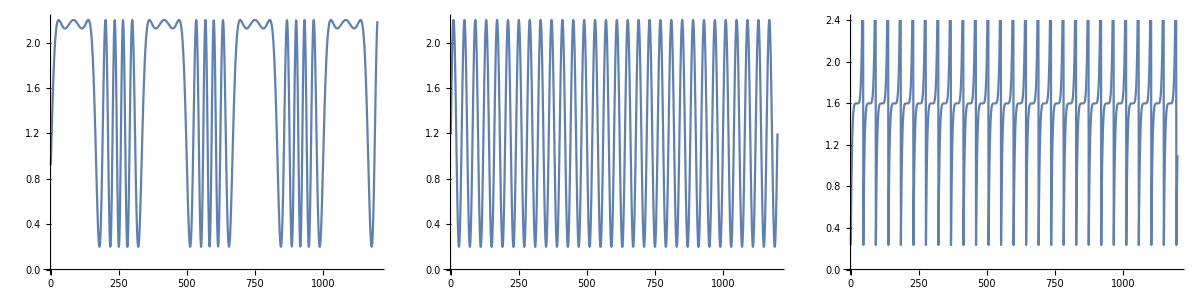

```mathematica
Grid[{Map[ListLinePlot[#,ImageSize->250]&,S]}]
```

#### Mixed signals matrix

```mathematica
M=A.S;
```

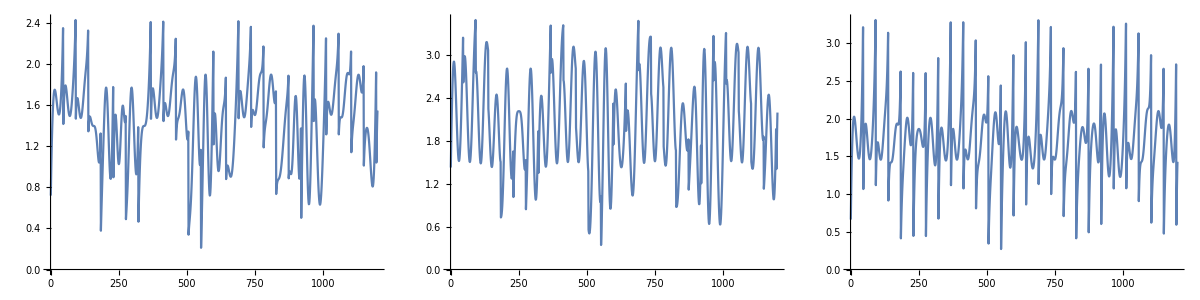

```mathematica
Grid[{Map[ListLinePlot[#,ImageSize->250]&,M]}]
```

### Using ICA for the cocktail party problem

```mathematica
X=Transpose[M];
```

```mathematica
{S,A}=IndependentComponentAnalysis[X,3];
```

```mathematica
res=FastICA[Transpose[M],3];
```

```mathematica
Norm[X-S.A]
```

3.58851×10^-14

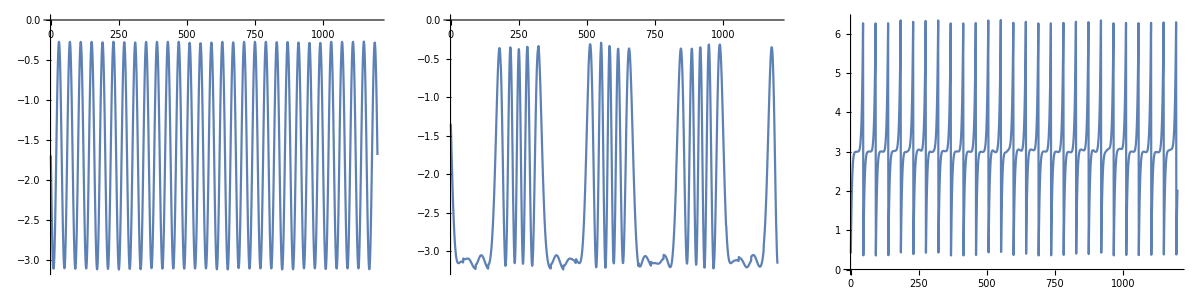

```mathematica
Grid[{Map[ListLinePlot[#,PlotRange->All,ImageSize->250]&,Transpose[S]]}]
```

[[ Include links from https://mathematica.stackexchange.com/a/115740/34008 ]]

### Using ICA for separating musical instruments from a recording

Blind source separation problem for an audio mix.

## Comparison of SVD, NNMF, and ICA over image de-noising

### Data

```mathematica
MNISTdigits=ExampleData[{"MachineLearning","MNIST"},"TestData"];
{testImages,testImageLabels}=Transpose[List@@@RandomSample[Cases[MNISTdigits,HoldPattern[(im_->0|4)]],100]];
testImages
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

See the breakdown of signal classes:

```mathematica
Tally[testImageLabels]
```

{{4,49},{0,51}}

Verify the images have the same sizes:

```mathematica
Tally[ImageDimensions/@testImages]
dims=%[[1,1]]
```

{{{28,28},100}}

{28,28}

Add different kinds of noise to the images:

```mathematica
noisyTestImages6=Table[ImageEffect[testImages[[i]],{RandomChoice[{"GaussianNoise","PoissonNoise","SaltPepperNoise"}],RandomReal[1]}],{i,Length[testImages]}];
RandomSample[Thread[{testImages,noisyTestImages6}],15]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Since the important values of the signals are 0 or close to 0 we negate the noisy images:

```mathematica
negNoisyTestImages6=ImageAdjust@*ColorNegate/@noisyTestImages6
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Linear vector space representation

TBD...

https://mathematica.stackexchange.com/a/114565/34008

### SVD dimension reduction

### NNMF

### ICA

### Comparison

```mathematica
Import["http://i.imgur.com/CrDlUJj.png"]
```

-Graphics-

### Further experiments

#### Gallery of experiments other digit pairs

#### Using Classify

```mathematica
Import["http://i.imgur.com/L7fLFiy.png"]
```

-Graphics-

### Links

[1] “Comparison of PCA and NNMF over image de-noising”

[2] “Comparison of PCA, NNMF, and ICA over image de-noising”

## Comparison of SVD, NNMF, and ICA over mandala images creation

“Comparison of dimension reduction algorithms over mandala images generation”

```mathematica
Import["http://i.imgur.com/l6mQ0Mv.png"]
```

-Graphics-

## Variable decisiveness through classification

This is a lengthy topic to be given in a talk of its own...

If I have time I am going to briefly go through the document / notebook:

“Importance of variables investigation guide.nb” .

GitHub link : “Importance of variables investigation guide” .

Blog post : “Importance of variables investigation” .

## References

[1] Anton Antonov, “MathematicaForPrediction utilities”, (2014), source code MathematicaForPrediction at GitHub,  https://github.com/antononcube/MathematicaForPrediction, package MathematicaForPredictionUtilities.m.

[2] Anton Antonov, Mosaic plot for data visualization implementation in Mathematica, (2014), MathematicaForPrediction at GitHub, package MosaicPlot.m.

[3] Anton Antonov, “Mosaic plots for data visualization”, (2014), MathematicaForPrediction at WordPress blog. URL: https://mathematicaforprediction.wordpress.com/2014/03/17/mosaic-plots-for-data-visualization/ .

[4] Anton Antonov, “MovieLens genre associations” (2013),  MathematicaForPrediction at GitHub, https://github.com/antononcube/MathematicaForPrediction, folder Documentation.

[5] Anton Antonov, Implementation of the Apriori algorithm in Mathematica, (2014), source code at MathematicaForPrediction at GitHub, package AprioriAlgorithm.m.

[6] Anton Antonov, "Topic and thesaurus extraction from a document collection" (2013),  MathematicaForPrediction at GitHub, https://github.com/antononcube/MathematicaForPrediction, folder Documentation.

[7] Anton Antonov, “Statistical thesaurus from NPR podcasts”, (2013), MathematicaForPrediction at WordPress blog. URL: https://mathematicaforprediction.wordpress.com/2013/10/15/statistical-thesaurus-from-npr-podcasts/ .

[8] Wikipedia entry, “Pareto principle”, URL: https://en.wikipedia.org/wiki/Pareto_principle .